```mathematica
(*Pictures for Algorithms in Grid Maze*)
```

```mathematica
path="/Users/moonstone/Dropbox/Documents/Research/Fun/GridMaze-Algorithm/pic/";
```

```mathematica
(*Euler Maze Definition*)
```

```mathematica
gapAngle[n_Integer]:=π/(6n);
twoAngles[n_Integer,a_]:=Block[{x=gapAngle[n]},{a-x,a+x}];
oneGapCircle[n_Integer,a_]:=Block[{sm=twoAngles[n,a]},Circle[{0,0},n,{sm⟦2⟧,sm⟦1⟧+2π}]];
NormalizeAngle[x_]:=If[x<0,NormalizeAngle[x+2π],If[x≥2π,NormalizeAngle[x-2π],x]];
CounterClockwiseCircle[r_,a_,b_]:=Block[{na=NormalizeAngle[a],nb=NormalizeAngle[b]},If[na<nb,Circle[{0,0},r,{na,nb}],Circle[{0,0},r,{na,nb+2π}]]];
twoGapsCircle[n_Integer,a_,b_]:=Block[{sm=Join[twoAngles[n,Min[a,b]],twoAngles[n,Max[a,b]]]},{CounterClockwiseCircle[n,sm[[2]],sm[[3]]],CounterClockwiseCircle[n,sm[[4]],sm[[1]]]}];
GenRandomAngle[n_Integer]:=Block[{result,last=RandomReal[2π],preLast=-1,i,r},
result={last};
For[i=1,i<n,i++,
r=RandomReal[2π];
While[(Abs[r-last]≤π/3)||(preLast>0&&(Abs[r-preLast]≤π/2)),r=RandomReal[2π]];
result=Append[result,r];
preLast=last;
last=r
];
result
];
channel[n_Integer,a_]:=Block[{sm1=twoAngles[n,a],sm2=twoAngles[n+1,a]},Line[{{{n Cos[sm1⟦1⟧],n Sin[sm1⟦1⟧]},{(n+1)Cos[sm2⟦1⟧],(n+1) Sin[sm2⟦1⟧]}},{{n Cos[sm1⟦2⟧],n Sin[sm1⟦2⟧]},{(n+1)Cos[sm2⟦2⟧],(n+1) Sin[sm2⟦2⟧]}}}]];
GenEulerMaze[mazeInput_,opt__]:=Graphics[{Thick,MapIndexed[twoGapsCircle[First[#2]+1,#1⟦1⟧,#1⟦2⟧]&,Partition[mazeInput,2,1]],oneGapCircle[1,First[mazeInput]],oneGapCircle[Length[mazeInput]+1,Last[mazeInput]],MapIndexed[channel[First[#2],#1]&,mazeInput]},opt]
```

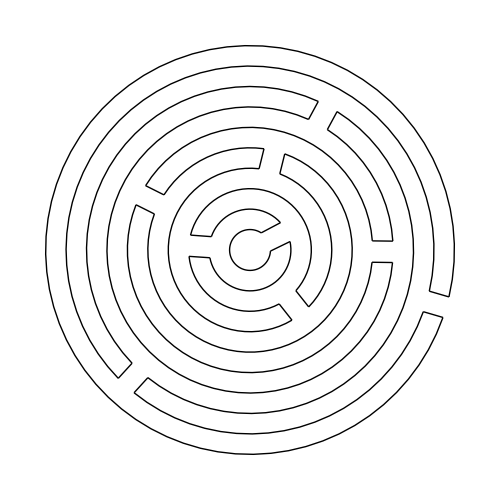

```mathematica
eulerCircleMaze=GenEulerMaze[GenRandomAngle[9],PlotRangePadding->None,ImageSize->500]
```

```mathematica
Export[path<>"eulerMaze.eps",eulerCircleMaze];
```

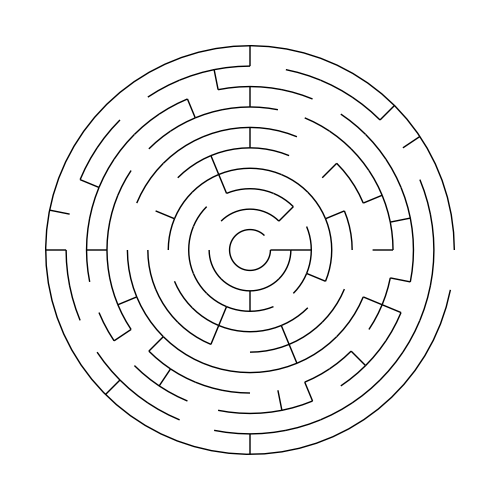

```mathematica
diskMaze=Graphics[{Thick,Line[{{1Cos[0Pi/8],1Sin[0Pi/8]},{2Cos[0Pi/8],2Sin[0Pi/8]}}],Line[{{2Cos[0Pi/8],2Sin[0Pi/8]},{3Cos[0Pi/8],3Sin[0Pi/8]}}],Line[{{2Cos[2Pi/8],2Sin[2Pi/8]},{3Cos[2Pi/8],3Sin[2Pi/8]}}],Line[{{2Cos[12Pi/8],2Sin[12Pi/8]},{3Cos[12Pi/8],3Sin[12Pi/8]}}],Line[{{3Cos[10Pi/16],3Sin[10Pi/16]},{4Cos[10Pi/16],4Sin[10Pi/16]}}],Line[{{3Cos[22Pi/16],3Sin[22Pi/16]},{4Cos[22Pi/16],4Sin[22Pi/16]}}],Line[{{3Cos[30Pi/16],3Sin[30Pi/16]},{4Cos[30Pi/16],4Sin[30Pi/16]}}],Line[{{4Cos[2Pi/16],4Sin[2Pi/16]},{5Cos[2Pi/16],5Sin[2Pi/16]}}],Line[{{4Cos[10Pi/16],4Sin[10Pi/16]},{5Cos[10Pi/16],5Sin[10Pi/16]}}],Line[{{4Cos[14Pi/16],4Sin[14Pi/16]},{5Cos[14Pi/16],5Sin[14Pi/16]}}],Line[{{4Cos[22Pi/16],4Sin[22Pi/16]},{5Cos[22Pi/16],5Sin[22Pi/16]}}],Line[{{4Cos[26Pi/16],4Sin[26Pi/16]},{5Cos[26Pi/16],5Sin[26Pi/16]}}],Line[{{5Cos[4Pi/16],5Sin[4Pi/16]},{6Cos[4Pi/16],6Sin[4Pi/16]}}],Line[{{5Cos[8Pi/16],5Sin[8Pi/16]},{6Cos[8Pi/16],6Sin[8Pi/16]}}],Line[{{5Cos[26Pi/16],5Sin[26Pi/16]},{6Cos[26Pi/16],6Sin[26Pi/16]}}],Line[{{6Cos[0Pi/16],6Sin[0Pi/16]},{7Cos[0Pi/16],7Sin[0Pi/16]}}],Line[{{6Cos[2Pi/16],6Sin[2Pi/16]},{7Cos[2Pi/16],7Sin[2Pi/16]}}],Line[{{6Cos[18Pi/16],6Sin[18Pi/16]},{7Cos[18Pi/16],7Sin[18Pi/16]}}],Line[{{6Cos[20Pi/16],6Sin[20Pi/16]},{7Cos[20Pi/16],7Sin[20Pi/16]}}],Line[{{6Cos[30Pi/16],6Sin[30Pi/16]},{7Cos[30Pi/16],7Sin[30Pi/16]}}],Line[{{7Cos[2Pi/32],7Sin[2Pi/32]},{8Cos[2Pi/32],8Sin[2Pi/32]}}],Line[{{7Cos[16Pi/32],7Sin[16Pi/32]},{8Cos[16Pi/32],8Sin[16Pi/32]}}],Line[{{7Cos[20Pi/32],7Sin[20Pi/32]},{8Cos[20Pi/32],8Sin[20Pi/32]}}],Line[{{7Cos[32Pi/32],7Sin[32Pi/32]},{8Cos[32Pi/32],8Sin[32Pi/32]}}],Line[{{7Cos[38Pi/32],7Sin[38Pi/32]},{8Cos[38Pi/32],8Sin[38Pi/32]}}],Line[{{7Cos[42Pi/32],7Sin[42Pi/32]},{8Cos[42Pi/32],8Sin[42Pi/32]}}],Line[{{7Cos[50Pi/32],7Sin[50Pi/32]},{8Cos[50Pi/32],8Sin[50Pi/32]}}],Line[{{7Cos[52Pi/32],7Sin[52Pi/32]},{8Cos[52Pi/32],8Sin[52Pi/32]}}],Line[{{7Cos[56Pi/32],7Sin[56Pi/32]},{8Cos[56Pi/32],8Sin[56Pi/32]}}],Line[{{7Cos[60Pi/32],7Sin[60Pi/32]},{8Cos[60Pi/32],8Sin[60Pi/32]}}],Line[{{7Cos[62Pi/32],7Sin[62Pi/32]},{8Cos[62Pi/32],8Sin[62Pi/32]}}],Line[{{8Cos[18Pi/32],8Sin[18Pi/32]},{9Cos[18Pi/32],9Sin[18Pi/32]}}],Line[{{8Cos[28Pi/32],8Sin[28Pi/32]},{9Cos[28Pi/32],9Sin[28Pi/32]}}],Line[{{9Cos[6Pi/32],9Sin[6Pi/32]},{10Cos[6Pi/32],10Sin[6Pi/32]}}],Line[{{9Cos[8Pi/32],9Sin[8Pi/32]},{10Cos[8Pi/32],10Sin[8Pi/32]}}],Line[{{9Cos[16Pi/32],9Sin[16Pi/32]},{10Cos[16Pi/32],10Sin[16Pi/32]}}],Line[{{9Cos[30Pi/32],9Sin[30Pi/32]},{10Cos[30Pi/32],10Sin[30Pi/32]}}],Line[{{9Cos[32Pi/32],9Sin[32Pi/32]},{10Cos[32Pi/32],10Sin[32Pi/32]}}],Line[{{9Cos[40Pi/32],9Sin[40Pi/32]},{10Cos[40Pi/32],10Sin[40Pi/32]}}],Line[{{9Cos[48Pi/32],9Sin[48Pi/32]},{10Cos[48Pi/32],10Sin[48Pi/32]}}],Circle[{0,0},2,{2Pi/8,4Pi/8}],Circle[{0,0},2,{4Pi/8,6Pi/8}],Circle[{0,0},2,{8Pi/8,10Pi/8}],Circle[{0,0},2,{10Pi/8,12Pi/8}],Circle[{0,0},2,{12Pi/8,14Pi/8}],Circle[{0,0},2,{14Pi/8,16Pi/8}],Circle[{0,0},3,{0Pi/16,2Pi/16}],Circle[{0,0},3,{4Pi/16,6Pi/16}],Circle[{0,0},3,{6Pi/16,8Pi/16}],Circle[{0,0},3,{8Pi/16,10Pi/16}],Circle[{0,0},3,{12Pi/16,14Pi/16}],Circle[{0,0},3,{14Pi/16,16Pi/16}],Circle[{0,0},3,{16Pi/16,18Pi/16}],Circle[{0,0},3,{18Pi/16,20Pi/16}],Circle[{0,0},3,{20Pi/16,22Pi/16}],Circle[{0,0},3,{22Pi/16,24Pi/16}],Circle[{0,0},3,{24Pi/16,26Pi/16}],Circle[{0,0},3,{28Pi/16,30Pi/16}],Circle[{0,0},3,{30Pi/16,32Pi/16}],Circle[{0,0},4,{0Pi/16,2Pi/16}],Circle[{0,0},4,{2Pi/16,4Pi/16}],Circle[{0,0},4,{4Pi/16,6Pi/16}],Circle[{0,0},4,{6Pi/16,8Pi/16}],Circle[{0,0},4,{8Pi/16,10Pi/16}],Circle[{0,0},4,{10Pi/16,12Pi/16}],Circle[{0,0},4,{12Pi/16,14Pi/16}],Circle[{0,0},4,{14Pi/16,16Pi/16}],Circle[{0,0},4,{18Pi/16,20Pi/16}],Circle[{0,0},4,{20Pi/16,22Pi/16}],Circle[{0,0},4,{22Pi/16,24Pi/16}],Circle[{0,0},4,{24Pi/16,26Pi/16}],Circle[{0,0},4,{26Pi/16,28Pi/16}],Circle[{0,0},4,{30Pi/16,32Pi/16}],Circle[{0,0},5,{0Pi/16,2Pi/16}],Circle[{0,0},5,{6Pi/16,8Pi/16}],Circle[{0,0},5,{8Pi/16,10Pi/16}],Circle[{0,0},5,{10Pi/16,12Pi/16}],Circle[{0,0},5,{16Pi/16,18Pi/16}],Circle[{0,0},5,{18Pi/16,20Pi/16}],Circle[{0,0},5,{20Pi/16,22Pi/16}],Circle[{0,0},5,{24Pi/16,26Pi/16}],Circle[{0,0},5,{26Pi/16,28Pi/16}],Circle[{0,0},5,{28Pi/16,30Pi/16}],Circle[{0,0},6,{2Pi/16,4Pi/16}],Circle[{0,0},6,{6Pi/16,8Pi/16}],Circle[{0,0},6,{8Pi/16,10Pi/16}],Circle[{0,0},6,{10Pi/16,12Pi/16}],Circle[{0,0},6,{12Pi/16,14Pi/16}],Circle[{0,0},6,{16Pi/16,18Pi/16}],Circle[{0,0},6,{18Pi/16,20Pi/16}],Circle[{0,0},6,{20Pi/16,22Pi/16}],Circle[{0,0},6,{22Pi/16,24Pi/16}],Circle[{0,0},6,{24Pi/16,26Pi/16}],Circle[{0,0},6,{26Pi/16,28Pi/16}],Circle[{0,0},6,{28Pi/16,30Pi/16}],Circle[{0,0},7,{0Pi/32,2Pi/32}],Circle[{0,0},7,{2Pi/32,4Pi/32}],Circle[{0,0},7,{4Pi/32,6Pi/32}],Circle[{0,0},7,{6Pi/32,8Pi/32}],Circle[{0,0},7,{8Pi/32,10Pi/32}],Circle[{0,0},7,{10Pi/32,12Pi/32}],Circle[{0,0},7,{14Pi/32,16Pi/32}],Circle[{0,0},7,{16Pi/32,18Pi/32}],Circle[{0,0},7,{18Pi/32,20Pi/32}],Circle[{0,0},7,{20Pi/32,22Pi/32}],Circle[{0,0},7,{22Pi/32,24Pi/32}],Circle[{0,0},7,{26Pi/32,28Pi/32}],Circle[{0,0},7,{28Pi/32,30Pi/32}],Circle[{0,0},7,{30Pi/32,32Pi/32}],Circle[{0,0},7,{32Pi/32,34Pi/32}],Circle[{0,0},7,{34Pi/32,36Pi/32}],Circle[{0,0},7,{36Pi/32,38Pi/32}],Circle[{0,0},7,{40Pi/32,42Pi/32}],Circle[{0,0},7,{42Pi/32,44Pi/32}],Circle[{0,0},7,{44Pi/32,46Pi/32}],Circle[{0,0},7,{46Pi/32,48Pi/32}],Circle[{0,0},7,{52Pi/32,54Pi/32}],Circle[{0,0},7,{54Pi/32,56Pi/32}],Circle[{0,0},7,{58Pi/32,60Pi/32}],Circle[{0,0},7,{60Pi/32,62Pi/32}],Circle[{0,0},8,{0Pi/32,2Pi/32}],Circle[{0,0},8,{2Pi/32,4Pi/32}],Circle[{0,0},8,{4Pi/32,6Pi/32}],Circle[{0,0},8,{6Pi/32,8Pi/32}],Circle[{0,0},8,{8Pi/32,10Pi/32}],Circle[{0,0},8,{12Pi/32,14Pi/32}],Circle[{0,0},8,{14Pi/32,16Pi/32}],Circle[{0,0},8,{16Pi/32,18Pi/32}],Circle[{0,0},8,{20Pi/32,22Pi/32}],Circle[{0,0},8,{22Pi/32,24Pi/32}],Circle[{0,0},8,{24Pi/32,26Pi/32}],Circle[{0,0},8,{26Pi/32,28Pi/32}],Circle[{0,0},8,{28Pi/32,30Pi/32}],Circle[{0,0},8,{30Pi/32,32Pi/32}],Circle[{0,0},8,{32Pi/32,34Pi/32}],Circle[{0,0},8,{36Pi/32,38Pi/32}],Circle[{0,0},8,{40Pi/32,42Pi/32}],Circle[{0,0},8,{42Pi/32,44Pi/32}],Circle[{0,0},8,{46Pi/32,48Pi/32}],Circle[{0,0},8,{48Pi/32,50Pi/32}],Circle[{0,0},8,{50Pi/32,52Pi/32}],Circle[{0,0},8,{54Pi/32,56Pi/32}],Circle[{0,0},8,{56Pi/32,58Pi/32}],Circle[{0,0},8,{58Pi/32,60Pi/32}],Circle[{0,0},8,{62Pi/32,64Pi/32}],Circle[{0,0},9,{0Pi/32,2Pi/32}],Circle[{0,0},9,{2Pi/32,4Pi/32}],Circle[{0,0},9,{8Pi/32,10Pi/32}],Circle[{0,0},9,{10Pi/32,12Pi/32}],Circle[{0,0},9,{12Pi/32,14Pi/32}],Circle[{0,0},9,{16Pi/32,18Pi/32}],Circle[{0,0},9,{18Pi/32,20Pi/32}],Circle[{0,0},9,{20Pi/32,22Pi/32}],Circle[{0,0},9,{24Pi/32,26Pi/32}],Circle[{0,0},9,{26Pi/32,28Pi/32}],Circle[{0,0},9,{32Pi/32,34Pi/32}],Circle[{0,0},9,{34Pi/32,36Pi/32}],Circle[{0,0},9,{38Pi/32,40Pi/32}],Circle[{0,0},9,{40Pi/32,42Pi/32}],Circle[{0,0},9,{42Pi/32,44Pi/32}],Circle[{0,0},9,{46Pi/32,48Pi/32}],Circle[{0,0},9,{48Pi/32,50Pi/32}],Circle[{0,0},9,{50Pi/32,52Pi/32}],Circle[{0,0},9,{52Pi/32,54Pi/32}],Circle[{0,0},9,{54Pi/32,56Pi/32}],Circle[{0,0},9,{56Pi/32,58Pi/32}],Circle[{0,0},9,{58Pi/32,60Pi/32}],Circle[{0,0},9,{60Pi/32,62Pi/32}],Circle[{0,0},9,{62Pi/32,64Pi/32}],Circle[{0,0},1,{2Pi/8,2Pi}],Circle[{0,0},10,{0Pi/32,62Pi/32}]},PlotRangePadding->None,ImageSize->500]
```

```mathematica
Export[path<>"diskMaze.eps",diskMaze]
```

/Users/moonstone/Dropbox/Documents/Research/Fun/GridMaze-Algorithm/pic/diskMaze.eps

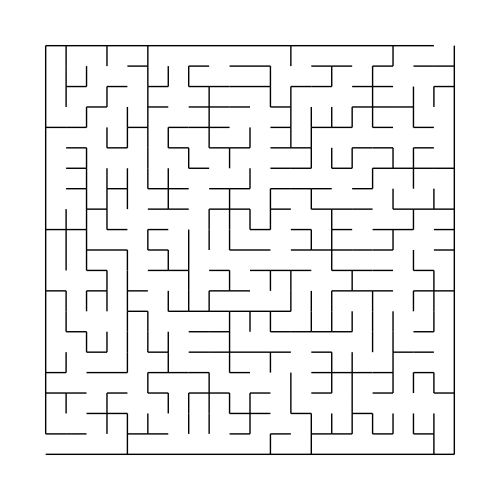

```mathematica
rectMaze=Graphics[{Thick,Line[{{4,0},{4,1}}],Line[{{11,0},{11,1}}],Line[{{13,0},{13,1}}],Line[{{19,0},{19,1}}],Line[{{3,1},{3,2}}],Line[{{4,1},{4,2}}],Line[{{5,1},{5,2}}],Line[{{7,1},{7,2}}],Line[{{8,1},{8,2}}],Line[{{10,1},{10,2}}],Line[{{13,1},{13,2}}],Line[{{14,1},{14,2}}],Line[{{15,1},{15,2}}],Line[{{16,1},{16,2}}],Line[{{17,1},{17,2}}],Line[{{18,1},{18,2}}],Line[{{19,1},{19,2}}],Line[{{1,2},{1,3}}],Line[{{3,2},{3,3}}],Line[{{6,2},{6,3}}],Line[{{7,2},{7,3}}],Line[{{8,2},{8,3}}],Line[{{9,2},{9,3}}],Line[{{10,2},{10,3}}],Line[{{12,2},{12,3}}],Line[{{15,2},{15,3}}],Line[{{5,3},{5,4}}],Line[{{8,3},{8,4}}],Line[{{12,3},{12,4}}],Line[{{14,3},{14,4}}],Line[{{15,3},{15,4}}],Line[{{17,3},{17,4}}],Line[{{18,3},{18,4}}],Line[{{19,3},{19,4}}],Line[{{1,4},{1,5}}],Line[{{4,4},{4,5}}],Line[{{6,4},{6,5}}],Line[{{9,4},{9,5}}],Line[{{11,4},{11,5}}],Line[{{14,4},{14,5}}],Line[{{15,4},{15,5}}],Line[{{17,4},{17,5}}],Line[{{2,5},{2,6}}],Line[{{3,5},{3,6}}],Line[{{4,5},{4,6}}],Line[{{5,5},{5,6}}],Line[{{6,5},{6,6}}],Line[{{9,5},{9,6}}],Line[{{16,5},{16,6}}],Line[{{17,5},{17,6}}],Line[{{1,6},{1,7}}],Line[{{4,6},{4,7}}],Line[{{5,6},{5,7}}],Line[{{9,6},{9,7}}],Line[{{10,6},{10,7}}],Line[{{11,6},{11,7}}],Line[{{13,6},{13,7}}],Line[{{14,6},{14,7}}],Line[{{15,6},{15,7}}],Line[{{16,6},{16,7}}],Line[{{17,6},{17,7}}],Line[{{19,6},{19,7}}],Line[{{1,7},{1,8}}],Line[{{2,7},{2,8}}],Line[{{3,7},{3,8}}],Line[{{4,7},{4,8}}],Line[{{6,7},{6,8}}],Line[{{7,7},{7,8}}],Line[{{8,7},{8,8}}],Line[{{12,7},{12,8}}],Line[{{13,7},{13,8}}],Line[{{14,7},{14,8}}],Line[{{16,7},{16,8}}],Line[{{18,7},{18,8}}],Line[{{19,7},{19,8}}],Line[{{3,8},{3,9}}],Line[{{4,8},{4,9}}],Line[{{7,8},{7,9}}],Line[{{9,8},{9,9}}],Line[{{11,8},{11,9}}],Line[{{12,8},{12,9}}],Line[{{15,8},{15,9}}],Line[{{19,8},{19,9}}],Line[{{1,9},{1,10}}],Line[{{2,9},{2,10}}],Line[{{4,9},{4,10}}],Line[{{6,9},{6,10}}],Line[{{7,9},{7,10}}],Line[{{14,9},{14,10}}],Line[{{18,9},{18,10}}],Line[{{1,10},{1,11}}],Line[{{2,10},{2,11}}],Line[{{5,10},{5,11}}],Line[{{7,10},{7,11}}],Line[{{8,10},{8,11}}],Line[{{9,10},{9,11}}],Line[{{13,10},{13,11}}],Line[{{14,10},{14,11}}],Line[{{17,10},{17,11}}],Line[{{1,11},{1,12}}],Line[{{2,11},{2,12}}],Line[{{3,11},{3,12}}],Line[{{8,11},{8,12}}],Line[{{9,11},{9,12}}],Line[{{10,11},{10,12}}],Line[{{11,11},{11,12}}],Line[{{14,11},{14,12}}],Line[{{18,11},{18,12}}],Line[{{2,12},{2,13}}],Line[{{3,12},{3,13}}],Line[{{4,12},{4,13}}],Line[{{6,12},{6,13}}],Line[{{9,12},{9,13}}],Line[{{11,12},{11,13}}],Line[{{13,12},{13,13}}],Line[{{17,12},{17,13}}],Line[{{19,12},{19,13}}],Line[{{2,13},{2,14}}],Line[{{3,13},{3,14}}],Line[{{4,13},{4,14}}],Line[{{5,13},{5,14}}],Line[{{6,13},{6,14}}],Line[{{10,13},{10,14}}],Line[{{16,13},{16,14}}],Line[{{18,13},{18,14}}],Line[{{2,14},{2,15}}],Line[{{5,14},{5,15}}],Line[{{7,14},{7,15}}],Line[{{9,14},{9,15}}],Line[{{13,14},{13,15}}],Line[{{14,14},{14,15}}],Line[{{15,14},{15,15}}],Line[{{17,14},{17,15}}],Line[{{18,14},{18,15}}],Line[{{3,15},{3,16}}],Line[{{4,15},{4,16}}],Line[{{5,15},{5,16}}],Line[{{6,15},{6,16}}],Line[{{8,15},{8,16}}],Line[{{10,15},{10,16}}],Line[{{12,15},{12,16}}],Line[{{13,15},{13,16}}],Line[{{2,16},{2,17}}],Line[{{4,16},{4,17}}],Line[{{5,16},{5,17}}],Line[{{8,16},{8,17}}],Line[{{12,16},{12,17}}],Line[{{13,16},{13,17}}],Line[{{14,16},{14,17}}],Line[{{15,16},{15,17}}],Line[{{16,16},{16,17}}],Line[{{18,16},{18,17}}],Line[{{1,17},{1,18}}],Line[{{3,17},{3,18}}],Line[{{5,17},{5,18}}],Line[{{8,17},{8,18}}],Line[{{11,17},{11,18}}],Line[{{12,17},{12,18}}],Line[{{16,17},{16,18}}],Line[{{18,17},{18,18}}],Line[{{19,17},{19,18}}],Line[{{1,18},{1,19}}],Line[{{2,18},{2,19}}],Line[{{5,18},{5,19}}],Line[{{6,18},{6,19}}],Line[{{7,18},{7,19}}],Line[{{11,18},{11,19}}],Line[{{14,18},{14,19}}],Line[{{16,18},{16,19}}],Line[{{1,19},{1,20}}],Line[{{3,19},{3,20}}],Line[{{5,19},{5,20}}],Line[{{12,19},{12,20}}],Line[{{17,19},{17,20}}],Line[{{0,1},{1,1}}],Line[{{1,1},{2,1}}],Line[{{4,1},{5,1}}],Line[{{5,1},{6,1}}],Line[{{9,1},{10,1}}],Line[{{11,1},{12,1}}],Line[{{13,1},{14,1}}],Line[{{14,1},{15,1}}],Line[{{16,1},{17,1}}],Line[{{18,1},{19,1}}],Line[{{2,2},{3,2}}],Line[{{3,2},{4,2}}],Line[{{9,2},{10,2}}],Line[{{10,2},{11,2}}],Line[{{12,2},{13,2}}],Line[{{15,2},{16,2}}],Line[{{0,3},{1,3}}],Line[{{1,3},{2,3}}],Line[{{3,3},{4,3}}],Line[{{5,3},{6,3}}],Line[{{7,3},{8,3}}],Line[{{8,3},{9,3}}],Line[{{10,3},{11,3}}],Line[{{13,3},{14,3}}],Line[{{16,3},{17,3}}],Line[{{19,3},{20,3}}],Line[{{0,4},{1,4}}],Line[{{2,4},{3,4}}],Line[{{3,4},{4,4}}],Line[{{5,4},{6,4}}],Line[{{6,4},{7,4}}],Line[{{7,4},{8,4}}],Line[{{9,4},{10,4}}],Line[{{13,4},{14,4}}],Line[{{14,4},{15,4}}],Line[{{15,4},{16,4}}],Line[{{16,4},{17,4}}],Line[{{18,4},{19,4}}],Line[{{2,5},{3,5}}],Line[{{5,5},{6,5}}],Line[{{7,5},{8,5}}],Line[{{8,5},{9,5}}],Line[{{9,5},{10,5}}],Line[{{10,5},{11,5}}],Line[{{11,5},{12,5}}],Line[{{13,5},{14,5}}],Line[{{17,5},{18,5}}],Line[{{18,5},{19,5}}],Line[{{1,6},{2,6}}],Line[{{7,6},{8,6}}],Line[{{8,6},{9,6}}],Line[{{11,6},{12,6}}],Line[{{12,6},{13,6}}],Line[{{13,6},{14,6}}],Line[{{14,6},{15,6}}],Line[{{18,6},{19,6}}],Line[{{4,7},{5,7}}],Line[{{6,7},{7,7}}],Line[{{7,7},{8,7}}],Line[{{8,7},{9,7}}],Line[{{9,7},{10,7}}],Line[{{10,7},{11,7}}],Line[{{11,7},{12,7}}],Line[{{0,8},{1,8}}],Line[{{2,8},{3,8}}],Line[{{4,8},{5,8}}],Line[{{8,8},{9,8}}],Line[{{9,8},{10,8}}],Line[{{14,8},{15,8}}],Line[{{15,8},{16,8}}],Line[{{16,8},{17,8}}],Line[{{18,8},{19,8}}],Line[{{19,8},{20,8}}],Line[{{2,9},{3,9}}],Line[{{5,9},{6,9}}],Line[{{6,9},{7,9}}],Line[{{8,9},{9,9}}],Line[{{10,9},{11,9}}],Line[{{11,9},{12,9}}],Line[{{12,9},{13,9}}],Line[{{14,9},{15,9}}],Line[{{15,9},{16,9}}],Line[{{16,9},{17,9}}],Line[{{18,9},{19,9}}],Line[{{2,10},{3,10}}],Line[{{3,10},{4,10}}],Line[{{5,10},{6,10}}],Line[{{9,10},{10,10}}],Line[{{10,10},{11,10}}],Line[{{12,10},{13,10}}],Line[{{13,10},{14,10}}],Line[{{14,10},{15,10}}],Line[{{15,10},{16,10}}],Line[{{16,10},{17,10}}],Line[{{19,10},{20,10}}],Line[{{0,11},{1,11}}],Line[{{1,11},{2,11}}],Line[{{3,11},{4,11}}],Line[{{5,11},{6,11}}],Line[{{10,11},{11,11}}],Line[{{12,11},{13,11}}],Line[{{14,11},{15,11}}],Line[{{16,11},{17,11}}],Line[{{17,11},{18,11}}],Line[{{19,11},{20,11}}],Line[{{2,12},{3,12}}],Line[{{5,12},{6,12}}],Line[{{6,12},{7,12}}],Line[{{8,12},{9,12}}],Line[{{9,12},{10,12}}],Line[{{11,12},{12,12}}],Line[{{13,12},{14,12}}],Line[{{14,12},{15,12}}],Line[{{15,12},{16,12}}],Line[{{17,12},{18,12}}],Line[{{18,12},{19,12}}],Line[{{19,12},{20,12}}],Line[{{1,13},{2,13}}],Line[{{3,13},{4,13}}],Line[{{5,13},{6,13}}],Line[{{6,13},{7,13}}],Line[{{8,13},{9,13}}],Line[{{9,13},{10,13}}],Line[{{11,13},{12,13}}],Line[{{12,13},{13,13}}],Line[{{13,13},{14,13}}],Line[{{15,13},{16,13}}],Line[{{1,14},{2,14}}],Line[{{7,14},{8,14}}],Line[{{11,14},{12,14}}],Line[{{12,14},{13,14}}],Line[{{14,14},{15,14}}],Line[{{16,14},{17,14}}],Line[{{17,14},{18,14}}],Line[{{18,14},{19,14}}],Line[{{19,14},{20,14}}],Line[{{1,15},{2,15}}],Line[{{3,15},{4,15}}],Line[{{6,15},{7,15}}],Line[{{8,15},{9,15}}],Line[{{9,15},{10,15}}],Line[{{11,15},{12,15}}],Line[{{12,15},{13,15}}],Line[{{15,15},{16,15}}],Line[{{16,15},{17,15}}],Line[{{18,15},{19,15}}],Line[{{0,16},{1,16}}],Line[{{1,16},{2,16}}],Line[{{4,16},{5,16}}],Line[{{6,16},{7,16}}],Line[{{7,16},{8,16}}],Line[{{8,16},{9,16}}],Line[{{11,16},{12,16}}],Line[{{13,16},{14,16}}],Line[{{14,16},{15,16}}],Line[{{16,16},{17,16}}],Line[{{18,16},{19,16}}],Line[{{2,17},{3,17}}],Line[{{5,17},{6,17}}],Line[{{7,17},{8,17}}],Line[{{8,17},{9,17}}],Line[{{9,17},{10,17}}],Line[{{11,17},{12,17}}],Line[{{15,17},{16,17}}],Line[{{16,17},{17,17}}],Line[{{17,17},{18,17}}],Line[{{1,18},{2,18}}],Line[{{3,18},{4,18}}],Line[{{5,18},{6,18}}],Line[{{7,18},{8,18}}],Line[{{8,18},{9,18}}],Line[{{9,18},{10,18}}],Line[{{10,18},{11,18}}],Line[{{12,18},{13,18}}],Line[{{13,18},{14,18}}],Line[{{15,18},{16,18}}],Line[{{16,18},{17,18}}],Line[{{19,18},{20,18}}],Line[{{4,19},{5,19}}],Line[{{7,19},{8,19}}],Line[{{9,19},{10,19}}],Line[{{10,19},{11,19}}],Line[{{13,19},{14,19}}],Line[{{14,19},{15,19}}],Line[{{16,19},{17,19}}],Line[{{18,19},{19,19}}],Line[{{19,19},{20,19}}],Line[{{0,1},{0,20}}],Line[{{0,20},{19,20}}],Line[{{20,20},{20,0}}],Line[{{20,0},{0,0}}]},PlotRangePadding->None,ImageSize->500]
```

```mathematica
Export[path<>"rectMaze.eps",rectMaze];
```

```mathematica
(*abcText Definition*)
```

```mathematica
abcText={{11,-9},{12,-9},{13,-9},{14,-9},{15,-9},{16,-9},{30,-9},{31,-9},{32,-9},{33,-9},{34,-9},{11,-10},{12,-10},{13,-10},{14,-10},{15,-10},{16,-10},{17,-10},{30,-10},{31,-10},{32,-10},{33,-10},{34,-10},{11,-11},{12,-11},{13,-11},{14,-11},{15,-11},{16,-11},{17,-11},{30,-11},{31,-11},{32,-11},{33,-11},{34,-11},{10,-12},{11,-12},{12,-12},{13,-12},{14,-12},{15,-12},{16,-12},{17,-12},{30,-12},{31,-12},{32,-12},{33,-12},{34,-12},{10,-13},{11,-13},{12,-13},{13,-13},{14,-13},{15,-13},{16,-13},{17,-13},{18,-13},{30,-13},{31,-13},{32,-13},{33,-13},{34,-13},{10,-14},{11,-14},{12,-14},{13,-14},{14,-14},{15,-14},{16,-14},{17,-14},{18,-14},{30,-14},{31,-14},{32,-14},{33,-14},{34,-14},{9,-15},{10,-15},{11,-15},{12,-15},{13,-15},{14,-15},{15,-15},{16,-15},{17,-15},{18,-15},{30,-15},{31,-15},{32,-15},{33,-15},{34,-15},{9,-16},{10,-16},{11,-16},{12,-16},{13,-16},{14,-16},{15,-16},{16,-16},{17,-16},{18,-16},{19,-16},{30,-16},{31,-16},{32,-16},{33,-16},{34,-16},{8,-17},{9,-17},{10,-17},{11,-17},{12,-17},{13,-17},{15,-17},{16,-17},{17,-17},{18,-17},{19,-17},{30,-17},{31,-17},{32,-17},{33,-17},{34,-17},{37,-17},{38,-17},{39,-17},{40,-17},{41,-17},{42,-17},{43,-17},{58,-17},{59,-17},{60,-17},{61,-17},{62,-17},{63,-17},{64,-17},{65,-17},{8,-18},{9,-18},{10,-18},{11,-18},{12,-18},{15,-18},{16,-18},{17,-18},{18,-18},{19,-18},{30,-18},{31,-18},{32,-18},{33,-18},{34,-18},{36,-18},{37,-18},{38,-18},{39,-18},{40,-18},{41,-18},{42,-18},{43,-18},{44,-18},{45,-18},{56,-18},{57,-18},{58,-18},{59,-18},{60,-18},{61,-18},{62,-18},{63,-18},{64,-18},{65,-18},{66,-18},{67,-18},{8,-19},{9,-19},{10,-19},{11,-19},{12,-19},{15,-19},{16,-19},{17,-19},{18,-19},{19,-19},{20,-19},{30,-19},{31,-19},{32,-19},{33,-19},{34,-19},{35,-19},{36,-19},{37,-19},{38,-19},{39,-19},{40,-19},{41,-19},{42,-19},{43,-19},{44,-19},{45,-19},{46,-19},{55,-19},{56,-19},{57,-19},{58,-19},{59,-19},{60,-19},{61,-19},{62,-19},{63,-19},{64,-19},{65,-19},{66,-19},{67,-19},{68,-19},{7,-20},{8,-20},{9,-20},{10,-20},{11,-20},{12,-20},{16,-20},{17,-20},{18,-20},{19,-20},{20,-20},{30,-20},{31,-20},{32,-20},{33,-20},{34,-20},{35,-20},{36,-20},{37,-20},{38,-20},{39,-20},{40,-20},{41,-20},{42,-20},{43,-20},{44,-20},{45,-20},{46,-20},{47,-20},{54,-20},{55,-20},{56,-20},{57,-20},{58,-20},{59,-20},{60,-20},{61,-20},{62,-20},{63,-20},{64,-20},{65,-20},{66,-20},{67,-20},{68,-20},{69,-20},{7,-21},{8,-21},{9,-21},{10,-21},{11,-21},{16,-21},{17,-21},{18,-21},{19,-21},{20,-21},{21,-21},{30,-21},{31,-21},{32,-21},{33,-21},{34,-21},{35,-21},{36,-21},{37,-21},{38,-21},{41,-21},{42,-21},{43,-21},{44,-21},{45,-21},{46,-21},{47,-21},{48,-21},{54,-21},{55,-21},{56,-21},{57,-21},{58,-21},{59,-21},{60,-21},{64,-21},{65,-21},{66,-21},{67,-21},{68,-21},{69,-21},{70,-21},{7,-22},{8,-22},{9,-22},{10,-22},{11,-22},{16,-22},{17,-22},{18,-22},{19,-22},{20,-22},{21,-22},{30,-22},{31,-22},{32,-22},{33,-22},{34,-22},{35,-22},{36,-22},{43,-22},{44,-22},{45,-22},{46,-22},{47,-22},{48,-22},{53,-22},{54,-22},{55,-22},{56,-22},{57,-22},{58,-22},{66,-22},{67,-22},{68,-22},{69,-22},{70,-22},{6,-23},{7,-23},{8,-23},{9,-23},{10,-23},{17,-23},{18,-23},{19,-23},{20,-23},{21,-23},{30,-23},{31,-23},{32,-23},{33,-23},{34,-23},{35,-23},{44,-23},{45,-23},{46,-23},{47,-23},{48,-23},{49,-23},{53,-23},{54,-23},{55,-23},{56,-23},{57,-23},{66,-23},{67,-23},{68,-23},{69,-23},{70,-23},{6,-24},{7,-24},{8,-24},{9,-24},{10,-24},{17,-24},{18,-24},{19,-24},{20,-24},{21,-24},{22,-24},{30,-24},{31,-24},{32,-24},{33,-24},{34,-24},{45,-24},{46,-24},{47,-24},{48,-24},{49,-24},{52,-24},{53,-24},{54,-24},{55,-24},{56,-24},{57,-24},{67,-24},{68,-24},{69,-24},{70,-24},{5,-25},{6,-25},{7,-25},{8,-25},{9,-25},{10,-25},{17,-25},{18,-25},{19,-25},{20,-25},{21,-25},{22,-25},{30,-25},{31,-25},{32,-25},{33,-25},{34,-25},{45,-25},{46,-25},{47,-25},{48,-25},{49,-25},{52,-25},{53,-25},{54,-25},{55,-25},{56,-25},{67,-25},{68,-25},{69,-25},{70,-25},{71,-25},{5,-26},{6,-26},{7,-26},{8,-26},{9,-26},{18,-26},{19,-26},{20,-26},{21,-26},{22,-26},{30,-26},{31,-26},{32,-26},{33,-26},{34,-26},{45,-26},{46,-26},{47,-26},{48,-26},{49,-26},{52,-26},{53,-26},{54,-26},{55,-26},{56,-26},{5,-27},{6,-27},{7,-27},{8,-27},{9,-27},{10,-27},{11,-27},{12,-27},{13,-27},{14,-27},{15,-27},{16,-27},{17,-27},{18,-27},{19,-27},{20,-27},{21,-27},{22,-27},{23,-27},{30,-27},{31,-27},{32,-27},{33,-27},{34,-27},{45,-27},{46,-27},{47,-27},{48,-27},{49,-27},{52,-27},{53,-27},{54,-27},{55,-27},{56,-27},{4,-28},{5,-28},{6,-28},{7,-28},{8,-28},{9,-28},{10,-28},{11,-28},{12,-28},{13,-28},{14,-28},{15,-28},{16,-28},{17,-28},{18,-28},{19,-28},{20,-28},{21,-28},{22,-28},{23,-28},{30,-28},{31,-28},{32,-28},{33,-28},{46,-28},{47,-28},{48,-28},{49,-28},{52,-28},{53,-28},{54,-28},{55,-28},{56,-28},{4,-29},{5,-29},{6,-29},{7,-29},{8,-29},{9,-29},{10,-29},{11,-29},{12,-29},{13,-29},{14,-29},{15,-29},{16,-29},{17,-29},{18,-29},{19,-29},{20,-29},{21,-29},{22,-29},{23,-29},{30,-29},{31,-29},{32,-29},{33,-29},{46,-29},{47,-29},{48,-29},{49,-29},{52,-29},{53,-29},{54,-29},{55,-29},{56,-29},{4,-30},{5,-30},{6,-30},{7,-30},{8,-30},{9,-30},{10,-30},{11,-30},{12,-30},{13,-30},{14,-30},{15,-30},{16,-30},{17,-30},{18,-30},{19,-30},{20,-30},{21,-30},{22,-30},{23,-30},{24,-30},{30,-30},{31,-30},{32,-30},{33,-30},{45,-30},{46,-30},{47,-30},{48,-30},{49,-30},{52,-30},{53,-30},{54,-30},{55,-30},{56,-30},{3,-31},{4,-31},{5,-31},{6,-31},{7,-31},{8,-31},{20,-31},{21,-31},{22,-31},{23,-31},{24,-31},{30,-31},{31,-31},{32,-31},{33,-31},{34,-31},{45,-31},{46,-31},{47,-31},{48,-31},{49,-31},{52,-31},{53,-31},{54,-31},{55,-31},{56,-31},{3,-32},{4,-32},{5,-32},{6,-32},{7,-32},{20,-32},{21,-32},{22,-32},{23,-32},{24,-32},{25,-32},{30,-32},{31,-32},{32,-32},{33,-32},{34,-32},{45,-32},{46,-32},{47,-32},{48,-32},{49,-32},{52,-32},{53,-32},{54,-32},{55,-32},{56,-32},{67,-32},{68,-32},{69,-32},{70,-32},{71,-32},{2,-33},{3,-33},{4,-33},{5,-33},{6,-33},{7,-33},{20,-33},{21,-33},{22,-33},{23,-33},{24,-33},{25,-33},{30,-33},{31,-33},{32,-33},{33,-33},{34,-33},{45,-33},{46,-33},{47,-33},{48,-33},{49,-33},{52,-33},{53,-33},{54,-33},{55,-33},{56,-33},{57,-33},{66,-33},{67,-33},{68,-33},{69,-33},{70,-33},{2,-34},{3,-34},{4,-34},{5,-34},{6,-34},{21,-34},{22,-34},{23,-34},{24,-34},{25,-34},{30,-34},{31,-34},{32,-34},{33,-34},{34,-34},{35,-34},{44,-34},{45,-34},{46,-34},{47,-34},{48,-34},{52,-34},{53,-34},{54,-34},{55,-34},{56,-34},{57,-34},{66,-34},{67,-34},{68,-34},{69,-34},{70,-34},{2,-35},{3,-35},{4,-35},{5,-35},{6,-35},{21,-35},{22,-35},{23,-35},{24,-35},{25,-35},{26,-35},{30,-35},{31,-35},{32,-35},{33,-35},{34,-35},{35,-35},{36,-35},{43,-35},{44,-35},{45,-35},{46,-35},{47,-35},{48,-35},{53,-35},{54,-35},{55,-35},{56,-35},{57,-35},{58,-35},{65,-35},{66,-35},{67,-35},{68,-35},{69,-35},{70,-35},{1,-36},{2,-36},{3,-36},{4,-36},{5,-36},{6,-36},{21,-36},{22,-36},{23,-36},{24,-36},{25,-36},{26,-36},{30,-36},{31,-36},{32,-36},{33,-36},{34,-36},{35,-36},{36,-36},{37,-36},{42,-36},{43,-36},{44,-36},{45,-36},{46,-36},{47,-36},{54,-36},{55,-36},{56,-36},{57,-36},{58,-36},{59,-36},{64,-36},{65,-36},{66,-36},{67,-36},{68,-36},{69,-36},{1,-37},{2,-37},{3,-37},{4,-37},{5,-37},{22,-37},{23,-37},{24,-37},{25,-37},{26,-37},{30,-37},{31,-37},{32,-37},{33,-37},{34,-37},{35,-37},{36,-37},{37,-37},{38,-37},{39,-37},{40,-37},{41,-37},{42,-37},{43,-37},{44,-37},{45,-37},{46,-37},{47,-37},{54,-37},{55,-37},{56,-37},{57,-37},{58,-37},{59,-37},{60,-37},{61,-37},{62,-37},{63,-37},{64,-37},{65,-37},{66,-37},{67,-37},{68,-37},{69,-37},{1,-38},{2,-38},{3,-38},{4,-38},{5,-38},{22,-38},{23,-38},{24,-38},{25,-38},{26,-38},{27,-38},{30,-38},{31,-38},{32,-38},{33,-38},{34,-38},{35,-38},{36,-38},{37,-38},{38,-38},{39,-38},{40,-38},{41,-38},{42,-38},{43,-38},{44,-38},{45,-38},{46,-38},{55,-38},{56,-38},{57,-38},{58,-38},{59,-38},{60,-38},{61,-38},{62,-38},{63,-38},{64,-38},{65,-38},{66,-38},{67,-38},{68,-38},{0,-39},{1,-39},{2,-39},{3,-39},{4,-39},{5,-39},{22,-39},{23,-39},{24,-39},{25,-39},{26,-39},{27,-39},{30,-39},{31,-39},{32,-39},{33,-39},{35,-39},{36,-39},{37,-39},{38,-39},{39,-39},{40,-39},{41,-39},{42,-39},{43,-39},{44,-39},{45,-39},{56,-39},{57,-39},{58,-39},{59,-39},{60,-39},{61,-39},{62,-39},{63,-39},{64,-39},{65,-39},{66,-39},{67,-39},{37,-40},{38,-40},{39,-40},{40,-40},{41,-40},{42,-40},{43,-40},{58,-40},{59,-40},{60,-40},{61,-40},{62,-40},{63,-40},{64,-40},{65,-40}};
```

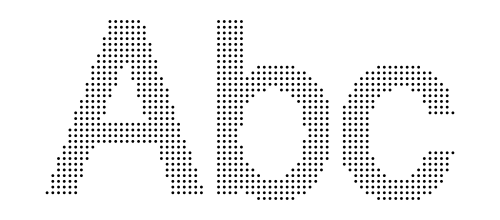

```mathematica
abcGrid=Graphics[Map[Disk[#,0.25]&,abcText],PlotRangePadding->None,ImageSize->500]
```

```mathematica
Export[path<>"abcGrid.eps",abcGrid];
```

```mathematica
(*abcSolution Definition*)
```

```mathematica
abcSolution={{71,-32},{70,-32},{70,-33},{69,-33},{69,-32},{68,-32},{68,-33},{67,-33},{66,-33},{66,-34},{67,-34},{67,-35},{68,-35},{68,-34},{69,-34},{70,-34},{70,-35},{69,-35},{69,-36},{69,-37},{68,-37},{68,-38},{68,-39},{67,-39},{67,-38},{66,-38},{66,-39},{65,-39},{65,-40},{64,-40},{64,-39},{63,-39},{63,-40},{62,-40},{62,-39},{62,-38},{63,-38},{64,-38},{65,-38},{65,-37},{66,-37},{67,-37},{67,-36},{66,-36},{66,-35},{65,-35},{65,-36},{64,-36},{64,-37},{63,-37},{62,-37},{61,-37},{61,-38},{61,-39},{61,-40},{60,-40},{60,-39},{60,-38},{60,-37},{60,-36},{59,-36},{58,-36},{57,-36},{57,-35},{58,-35},{58,-34},{57,-34},{56,-34},{56,-35},{56,-36},{56,-37},{57,-37},{57,-38},{58,-38},{58,-37},{59,-37},{59,-38},{59,-39},{59,-40},{58,-40},{58,-39},{57,-39},{56,-39},{56,-38},{55,-38},{55,-37},{54,-37},{54,-36},{55,-36},{55,-35},{55,-34},{55,-33},{56,-33},{57,-33},{57,-32},{56,-32},{56,-31},{56,-30},{55,-30},{55,-31},{55,-32},{54,-32},{54,-31},{54,-30},{54,-29},{54,-28},{54,-27},{54,-26},{55,-26},{55,-27},{55,-28},{55,-29},{56,-29},{56,-28},{56,-27},{56,-26},{56,-25},{55,-25},{54,-25},{54,-24},{55,-24},{55,-23},{56,-23},{56,-24},{57,-24},{57,-23},{57,-22},{58,-22},{59,-22},{59,-21},{59,-20},{60,-20},{60,-21},{61,-21},{61,-20},{62,-20},{63,-20},{63,-19},{64,-19},{64,-20},{64,-21},{65,-21},{65,-20},{66,-20},{66,-21},{66,-22},{67,-22},{67,-23},{67,-24},{67,-25},{68,-25},{68,-24},{69,-24},{69,-25},{70,-25},{71,-25},{71,-24},{70,-24},{70,-23},{70,-22},{70,-21},{70,-20},{69,-20},{69,-21},{69,-22},{69,-23},{68,-23},{68,-22},{68,-21},{67,-21},{67,-20},{68,-20},{68,-19},{67,-19},{67,-18},{66,-18},{66,-19},{65,-19},{65,-18},{65,-17},{64,-17},{64,-18},{63,-18},{63,-17},{62,-17},{62,-18},{62,-19},{61,-19},{61,-18},{61,-17},{60,-17},{60,-18},{60,-19},{59,-19},{59,-18},{59,-17},{58,-17},{58,-18},{58,-19},{57,-19},{57,-18},{56,-18},{56,-19},{55,-19},{54,-19},{54,-20},{55,-20},{56,-20},{57,-20},{58,-20},{58,-21},{57,-21},{56,-21},{56,-22},{55,-22},{55,-21},{54,-21},{54,-22},{53,-22},{53,-23},{53,-24},{53,-25},{53,-26},{53,-27},{53,-28},{53,-29},{53,-30},{53,-31},{53,-32},{53,-33},{54,-33},{54,-34},{54,-35},{53,-35},{53,-34},{52,-34},{52,-33},{52,-32},{52,-31},{52,-30},{52,-29},{52,-28},{52,-27},{52,-26},{52,-25},{52,-24},{51,-24},{50,-24},{50,-23},{49,-23},{48,-23},{48,-24},{49,-24},{49,-25},{48,-25},{47,-25},{47,-24},{47,-23},{46,-23},{46,-24},{46,-25},{46,-26},{47,-26},{48,-26},{49,-26},{49,-27},{48,-27},{47,-27},{47,-28},{48,-28},{49,-28},{49,-29},{49,-30},{49,-31},{48,-31},{48,-30},{48,-29},{47,-29},{47,-30},{47,-31},{47,-32},{48,-32},{49,-32},{49,-33},{48,-33},{48,-34},{48,-35},{47,-35},{47,-34},{47,-33},{46,-33},{46,-34},{46,-35},{46,-36},{47,-36},{47,-37},{46,-37},{46,-38},{46,-39},{45,-39},{45,-38},{45,-37},{45,-36},{44,-36},{44,-37},{44,-38},{44,-39},{43,-39},{43,-40},{42,-40},{42,-39},{42,-38},{43,-38},{43,-37},{42,-37},{42,-36},{43,-36},{43,-35},{44,-35},{44,-34},{45,-34},{45,-33},{45,-32},{46,-32},{46,-31},{45,-31},{45,-30},{46,-30},{46,-29},{46,-28},{46,-27},{45,-27},{45,-26},{45,-25},{45,-24},{45,-23},{44,-23},{43,-23},{43,-22},{43,-21},{42,-21},{41,-21},{41,-20},{42,-20},{43,-20},{44,-20},{44,-21},{44,-22},{45,-22},{46,-22},{47,-22},{48,-22},{48,-21},{47,-21},{46,-21},{45,-21},{45,-20},{46,-20},{46,-19},{45,-19},{45,-18},{44,-18},{44,-19},{43,-19},{42,-19},{42,-18},{43,-18},{43,-17},{42,-17},{41,-17},{40,-17},{39,-17},{38,-17},{37,-17},{37,-18},{38,-18},{38,-19},{39,-19},{39,-18},{40,-18},{41,-18},{41,-19},{40,-19},{40,-20},{39,-20},{38,-20},{38,-21},{37,-21},{37,-20},{36,-20},{36,-19},{36,-18},{35,-18},{35,-19},{35,-20},{35,-21},{36,-21},{36,-22},{35,-22},{35,-23},{35,-24},{34,-24},{34,-23},{34,-22},{34,-21},{34,-20},{34,-19},{34,-18},{33,-18},{33,-19},{33,-20},{33,-21},{33,-22},{32,-22},{32,-23},{33,-23},{33,-24},{33,-25},{34,-25},{34,-26},{34,-27},{33,-27},{33,-28},{33,-29},{33,-30},{33,-31},{34,-31},{34,-32},{33,-32},{33,-33},{34,-33},{35,-33},{35,-34},{34,-34},{33,-34},{33,-35},{34,-35},{34,-36},{33,-36},{33,-37},{34,-37},{35,-37},{36,-37},{36,-36},{35,-36},{35,-35},{36,-35},{37,-35},{37,-36},{37,-37},{38,-37},{39,-37},{40,-37},{41,-37},{41,-38},{41,-39},{41,-40},{40,-40},{40,-39},{40,-38},{39,-38},{39,-39},{39,-40},{38,-40},{38,-39},{38,-38},{37,-38},{37,-39},{37,-40},{36,-40},{36,-39},{36,-38},{35,-38},{35,-39},{34,-39},{34,-38},{33,-38},{33,-39},{32,-39},{32,-38},{32,-37},{32,-36},{32,-35},{32,-34},{32,-33},{32,-32},{32,-31},{32,-30},{32,-29},{32,-28},{32,-27},{32,-26},{32,-25},{32,-24},{31,-24},{31,-23},{31,-22},{31,-21},{32,-21},{32,-20},{31,-20},{31,-19},{32,-19},{32,-18},{31,-18},{31,-17},{31,-16},{32,-16},{32,-17},{33,-17},{34,-17},{34,-16},{34,-15},{34,-14},{34,-13},{34,-12},{34,-11},{34,-10},{34,-9},{33,-9},{33,-10},{33,-11},{33,-12},{33,-13},{33,-14},{33,-15},{32,-15},{31,-15},{31,-14},{32,-14},{32,-13},{32,-12},{32,-11},{32,-10},{32,-9},{31,-9},{30,-9},{30,-10},{31,-10},{31,-11},{30,-11},{30,-12},{31,-12},{31,-13},{30,-13},{30,-14},{30,-15},{30,-16},{30,-17},{30,-18},{30,-19},{30,-20},{30,-21},{30,-22},{30,-23},{30,-24},{30,-25},{31,-25},{31,-26},{30,-26},{30,-27},{31,-27},{31,-28},{30,-28},{30,-29},{31,-29},{31,-30},{30,-30},{30,-31},{31,-31},{31,-32},{30,-32},{30,-33},{31,-33},{31,-34},{30,-34},{30,-35},{31,-35},{31,-36},{30,-36},{30,-37},{31,-37},{31,-38},{31,-39},{30,-39},{30,-38},{29,-38},{28,-38},{27,-38},{27,-39},{26,-39},{26,-38},{26,-37},{26,-36},{26,-35},{25,-35},{25,-36},{25,-37},{24,-37},{24,-38},{25,-38},{25,-39},{24,-39},{23,-39},{22,-39},{22,-38},{22,-37},{23,-37},{23,-36},{24,-36},{24,-35},{23,-35},{22,-35},{22,-36},{21,-36},{21,-35},{21,-34},{20,-34},{20,-33},{20,-32},{20,-31},{20,-30},{19,-30},{19,-29},{19,-28},{19,-27},{20,-27},{20,-26},{19,-26},{18,-26},{18,-27},{17,-27},{16,-27},{15,-27},{14,-27},{14,-28},{15,-28},{16,-28},{17,-28},{18,-28},{18,-29},{18,-30},{17,-30},{17,-29},{16,-29},{16,-30},{15,-30},{15,-29},{14,-29},{14,-30},{13,-30},{12,-30},{11,-30},{11,-29},{10,-29},{10,-30},{9,-30},{9,-29},{9,-28},{10,-28},{11,-28},{12,-28},{12,-29},{13,-29},{13,-28},{13,-27},{12,-27},{11,-27},{10,-27},{9,-27},{9,-26},{8,-26},{8,-25},{8,-24},{8,-23},{9,-23},{9,-24},{9,-25},{10,-25},{10,-24},{10,-23},{10,-22},{11,-22},{11,-21},{11,-20},{12,-20},{12,-19},{11,-19},{10,-19},{9,-19},{9,-18},{10,-18},{11,-18},{12,-18},{12,-17},{11,-17},{10,-17},{10,-16},{11,-16},{12,-16},{12,-15},{13,-15},{13,-16},{13,-17},{14,-17},{14,-16},{15,-16},{15,-17},{16,-17},{16,-18},{15,-18},{15,-19},{16,-19},{17,-19},{18,-19},{18,-20},{17,-20},{16,-20},{16,-21},{17,-21},{17,-22},{16,-22},{16,-23},{17,-23},{18,-23},{18,-24},{17,-24},{17,-25},{18,-25},{19,-25},{19,-24},{20,-24},{20,-25},{21,-25},{21,-26},{21,-27},{21,-28},{20,-28},{20,-29},{21,-29},{21,-30},{21,-31},{21,-32},{21,-33},{22,-33},{22,-34},{23,-34},{23,-33},{24,-33},{24,-34},{25,-34},{25,-33},{25,-32},{24,-32},{24,-31},{23,-31},{23,-32},{22,-32},{22,-31},{22,-30},{23,-30},{23,-29},{22,-29},{22,-28},{23,-28},{23,-27},{22,-27},{22,-26},{22,-25},{22,-24},{21,-24},{21,-23},{21,-22},{21,-21},{20,-21},{20,-22},{20,-23},{19,-23},{19,-22},{18,-22},{18,-21},{19,-21},{19,-20},{20,-20},{20,-19},{19,-19},{19,-18},{19,-17},{19,-16},{18,-16},{18,-17},{18,-18},{17,-18},{17,-17},{17,-16},{16,-16},{16,-15},{15,-15},{14,-15},{14,-14},{15,-14},{16,-14},{17,-14},{17,-15},{18,-15},{18,-14},{18,-13},{17,-13},{17,-12},{17,-11},{17,-10},{16,-10},{16,-9},{15,-9},{14,-9},{14,-10},{15,-10},{15,-11},{15,-12},{16,-12},{16,-13},{15,-13},{14,-13},{13,-13},{13,-14},{12,-14},{11,-14},{11,-13},{12,-13},{12,-12},{13,-12},{14,-12},{14,-11},{13,-11},{12,-11},{12,-10},{13,-10},{13,-9},{12,-9},{11,-9},{11,-10},{11,-11},{11,-12},{10,-12},{10,-13},{10,-14},{10,-15},{9,-15},{9,-16},{9,-17},{8,-17},{8,-18},{8,-19},{7,-19},{7,-20},{8,-20},{9,-20},{10,-20},{10,-21},{9,-21},{9,-22},{8,-22},{8,-21},{7,-21},{7,-22},{7,-23},{6,-23},{6,-24},{7,-24},{7,-25},{7,-26},{6,-26},{6,-25},{5,-25},{5,-26},{5,-27},{6,-27},{6,-28},{7,-28},{7,-27},{8,-27},{8,-28},{8,-29},{7,-29},{7,-30},{8,-30},{8,-31},{7,-31},{7,-32},{7,-33},{7,-34},{6,-34},{6,-33},{6,-32},{6,-31},{6,-30},{6,-29},{5,-29},{5,-28},{4,-28},{4,-29},{4,-30},{5,-30},{5,-31},{5,-32},{5,-33},{5,-34},{5,-35},{6,-35},{6,-36},{5,-36},{5,-37},{5,-38},{5,-39},{4,-39},{4,-38},{4,-37},{4,-36},{4,-35},{4,-34},{4,-33},{4,-32},{4,-31},{3,-31},{3,-32},{2,-32},{2,-33},{3,-33},{3,-34},{2,-34},{2,-35},{3,-35},{3,-36},{3,-37},{3,-38},{3,-39},{2,-39},{2,-38},{2,-37},{2,-36},{1,-36},{1,-37},{1,-38},{1,-39},{0,-39}};
```

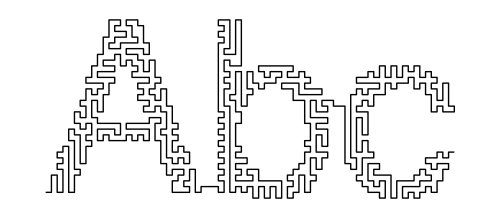

```mathematica
abcPath=Graphics[{Line[abcSolution]},PlotRangePadding->None,ImageSize->500]
```

```mathematica
Export[path<>"abcPath.eps",abcPath];
```

```mathematica
rectGraph={Map[Disk[#,0.2]&,Flatten[Table[{i+1/2,j+1/2},{i,0,19},{j,0,19}],1]],Thick,Line[Table[{{1/2,i+1/2},{39/2,i+1/2}},{i,0,19}]],Line[Table[{{i+1/2,1/2},{i+1/2,39/2}},{i,0,19}]]};
```

```mathematica
Export[path<>"rectGraph.eps",Graphics[rectGraph,PlotRangePadding->None,ImageSize->500]];
```

```mathematica
rectCells={Line[Table[{{0,i},{20,i}},{i,0,20}]],Line[Table[{{i,0},{i,20}},{i,0,20}]]};
```

```mathematica
Export[path<>"rectCells.eps",Graphics[rectCells,PlotRangePadding->None,ImageSize->500]];
```

```mathematica
rectMerged=Graphics[{Gray,rectGraph,Black,Thickness[Medium],rectCells},PlotRangePadding->None,ImageSize->500]
```

-Graphics-

```mathematica
Export[path<>"rectMerged.eps",rectMerged];
```

```mathematica
diskWall[ang_,sR_,eR_]:= Line[{{sR Cos[ang],sR Sin[ang]},{eR Cos[ang],eR Sin[ang]}}]
```

```mathematica
forkWall[ang_,sR_,eR_,diffAng_]:=Line[Table[{{sR Cos[ang],sR Sin[ang]},{eR Cos[ang+i],eR Sin[ang+i]}},{i,{-diffAng,diffAng}}]]
```

```mathematica
diskGraph={Map[Disk[#,0.2]&,Flatten[Table[Map[{r Cos[#],r Sin[#]}&,Table[i+π/8,{i,0,2π-π/8,π/4}]],{r,3/2,5/2,1}],1]],
Map[Disk[#,0.2]&,Flatten[Table[Map[{r Cos[#],r Sin[#]}&,Table[i+π/16,{i,0,2π-π/16,π/8}]],{r,3+1/2,7-1/2,1}],1]],
Map[Disk[#,0.2]&,Flatten[Table[Map[{r Cos[#],r Sin[#]}&,Table[i+π/32,{i,0,2π-π/32,π/16}]],{r,7+1/2,10-1/2,1}],1]],
Thick,
Table[Circle[{0,0},i+1/2],{i,1,9}],
Table[diskWall[i+π/8,3/2,5/2],{i,0,2π-π/8,π/4}],
Table[diskWall[i+π/16,3+1/2,7-1/2],{i,0,2π-π/16,π/8}],
Table[diskWall[i+π/32,7+1/2,10-1/2],{i,0,2π-π/32,π/16}],
Table[forkWall[i+π/8,5/2,3+1/2,π/16],{i,0,2π-π/8,π/4}],
Table[forkWall[i+π/16,7-1/2,7+1/2,π/32],{i,0,2π-π/16,π/8}]};
```

```mathematica
Export[path<>"diskGraph.eps",Graphics[diskGraph,PlotRangePadding->None,ImageSize->500]];
```

```mathematica
diskCells={Table[Circle[{0,0},i],{i,1,10}],
Table[diskWall[i,1,10],{i,0,2π-π/4,π/4}],
Table[diskWall[i,3,10],{i,π/8,2π-π/8,π/4}],
Table[diskWall[i,7,10],{i,π/16,2π-π/16,π/8}]};
```

```mathematica
Export[path<>"diskCells.eps",Graphics[diskCells,PlotRangePadding->None,ImageSize->500]];
```

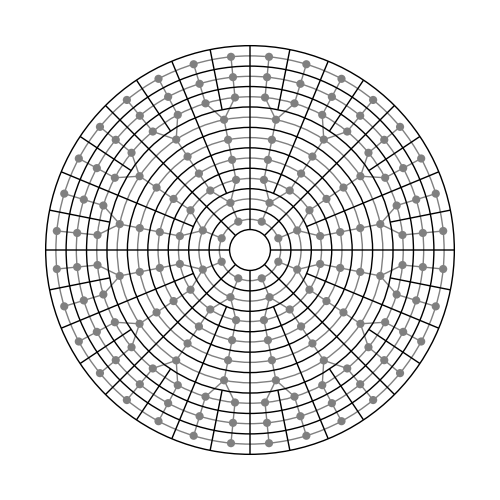

```mathematica
diskMerged=Graphics[{Gray,diskGraph,Black,Thickness[Medium],diskCells},PlotRangePadding->None,ImageSize->500]
```

```mathematica
Export[path<>"diskMerged.eps",diskMerged];
```

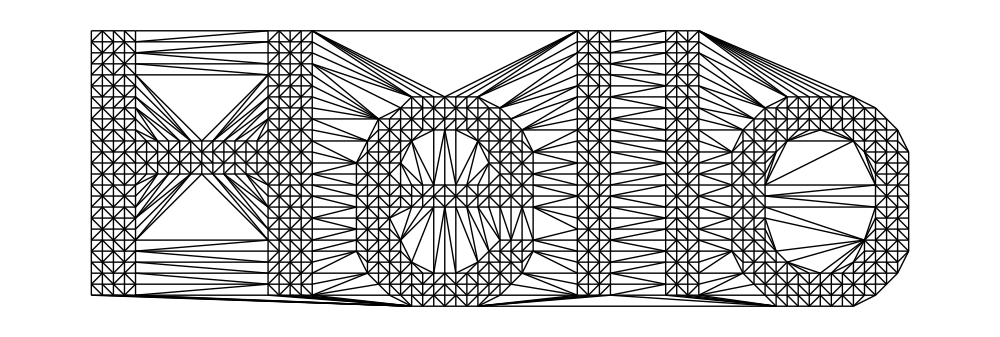

```mathematica
helloTri=Graphics[Line[{{{2,-8},{2,-9}},{{2,-8},{3,-8}},{{3,-8},{3,-9}},{{3,-8},{2,-9}},{{3,-8},{4,-9}},{{3,-8},{4,-8}},{{4,-8},{4,-9}},{{4,-8},{5,-9}},{{4,-8},{5,-8}},{{5,-8},{5,-9}},{{5,-8},{6,-9}},{{5,-8},{6,-8}},{{6,-8},{6,-9}},{{6,-8},{18,-8}},{{18,-8},{6,-9}},{{18,-8},{18,-9}},{{18,-8},{19,-8}},{{19,-8},{18,-9}},{{19,-8},{19,-9}},{{19,-8},{20,-9}},{{19,-8},{20,-8}},{{20,-8},{20,-9}},{{20,-8},{21,-8}},{{21,-8},{20,-9}},{{21,-8},{21,-9}},{{21,-8},{22,-8}},{{22,-8},{21,-9}},{{22,-8},{22,-9}},{{22,-8},{31,-14}},{{22,-8},{32,-14}},{{22,-8},{33,-14}},{{22,-8},{34,-14}},{{22,-8},{46,-8}},{{46,-8},{34,-14}},{{46,-8},{35,-14}},{{46,-8},{36,-14}},{{46,-8},{37,-14}},{{46,-8},{46,-9}},{{46,-8},{47,-8}},{{46,-8},{47,-9}},{{47,-8},{48,-8}},{{47,-8},{47,-9}},{{48,-8},{48,-9}},{{48,-8},{49,-9}},{{48,-8},{49,-8}},{{48,-8},{47,-9}},{{49,-8},{49,-9}},{{49,-8},{54,-8}},{{54,-8},{49,-9}},{{54,-8},{54,-9}},{{54,-8},{55,-8}},{{55,-8},{54,-9}},{{55,-8},{55,-9}},{{55,-8},{56,-9}},{{55,-8},{56,-8}},{{56,-8},{56,-9}},{{56,-8},{57,-8}},{{57,-8},{56,-9}},{{57,-8},{57,-9}},{{57,-8},{65,-14}},{{57,-8},{66,-14}},{{57,-8},{67,-14}},{{57,-8},{68,-14}},{{57,-8},{69,-14}},{{57,-8},{70,-14}},{{57,-8},{71,-14}},{{2,-9},{2,-10}},{{2,-9},{3,-9}},{{2,-9},{3,-10}},{{3,-9},{4,-9}},{{3,-9},{3,-10}},{{4,-9},{5,-9}},{{4,-9},{4,-10}},{{4,-9},{3,-10}},{{5,-9},{5,-10}},{{5,-9},{4,-10}},{{5,-9},{6,-9}},{{5,-9},{6,-10}},{{6,-9},{18,-9}},{{6,-9},{6,-10}},{{18,-9},{18,-10}},{{18,-9},{6,-10}},{{18,-9},{19,-10}},{{18,-9},{19,-9}},{{19,-9},{19,-10}},{{19,-9},{20,-10}},{{19,-9},{20,-9}},{{20,-9},{20,-10}},{{20,-9},{21,-9}},{{21,-9},{20,-10}},{{21,-9},{21,-10}},{{21,-9},{22,-9}},{{22,-9},{21,-10}},{{22,-9},{22,-10}},{{22,-9},{31,-14}},{{46,-9},{37,-14}},{{46,-9},{46,-10}},{{46,-9},{47,-9}},{{47,-9},{46,-10}},{{47,-9},{47,-10}},{{47,-9},{48,-10}},{{47,-9},{48,-9}},{{48,-9},{48,-10}},{{48,-9},{49,-10}},{{48,-9},{49,-9}},{{49,-9},{49,-10}},{{49,-9},{54,-9}},{{54,-9},{49,-10}},{{54,-9},{54,-10}},{{54,-9},{55,-9}},{{55,-9},{54,-10}},{{55,-9},{55,-10}},{{55,-9},{56,-10}},{{55,-9},{56,-9}},{{56,-9},{56,-10}},{{56,-9},{57,-9}},{{57,-9},{56,-10}},{{57,-9},{57,-10}},{{57,-9},{65,-14}},{{2,-10},{3,-10}},{{2,-10},{2,-11}},{{3,-10},{4,-10}},{{3,-10},{3,-11}},{{3,-10},{2,-11}},{{4,-10},{4,-11}},{{4,-10},{3,-11}},{{4,-10},{5,-10}},{{4,-10},{5,-11}},{{5,-10},{6,-10}},{{5,-10},{5,-11}},{{6,-10},{6,-11}},{{6,-10},{5,-11}},{{6,-10},{18,-11}},{{6,-10},{18,-10}},{{18,-10},{18,-11}},{{18,-10},{19,-10}},{{19,-10},{19,-11}},{{19,-10},{18,-11}},{{19,-10},{20,-10}},{{20,-10},{19,-11}},{{20,-10},{20,-11}},{{20,-10},{21,-11}},{{20,-10},{21,-10}},{{21,-10},{21,-11}},{{21,-10},{22,-10}},{{22,-10},{31,-14}},{{22,-10},{21,-11}},{{22,-10},{22,-11}},{{46,-10},{37,-14}},{{46,-10},{47,-10}},{{46,-10},{39,-15}},{{46,-10},{46,-11}},{{47,-10},{46,-11}},{{47,-10},{47,-11}},{{47,-10},{48,-11}},{{47,-10},{48,-10}},{{48,-10},{48,-11}},{{48,-10},{49,-10}},{{48,-10},{49,-11}},{{49,-10},{54,-10}},{{49,-10},{49,-11}},{{54,-10},{54,-11}},{{54,-10},{49,-11}},{{54,-10},{55,-11}},{{54,-10},{55,-10}},{{55,-10},{55,-11}},{{55,-10},{56,-10}},{{56,-10},{55,-11}},{{56,-10},{56,-11}},{{56,-10},{57,-10}},{{57,-10},{65,-14}},{{57,-10},{63,-15}},{{57,-10},{56,-11}},{{57,-10},{57,-11}},{{2,-11},{2,-12}},{{2,-11},{3,-11}},{{3,-11},{2,-12}},{{3,-11},{3,-12}},{{3,-11},{4,-12}},{{3,-11},{4,-11}},{{4,-11},{4,-12}},{{4,-11},{5,-11}},{{5,-11},{6,-12}},{{5,-11},{6,-11}},{{5,-11},{4,-12}},{{5,-11},{5,-12}},{{6,-11},{6,-12}},{{6,-11},{18,-12}},{{6,-11},{18,-11}},{{18,-11},{18,-12}},{{18,-11},{19,-11}},{{19,-11},{19,-12}},{{19,-11},{18,-12}},{{19,-11},{20,-12}},{{19,-11},{20,-11}},{{20,-11},{20,-12}},{{20,-11},{21,-11}},{{21,-11},{22,-11}},{{21,-11},{20,-12}},{{21,-11},{21,-12}},{{21,-11},{22,-12}},{{22,-11},{31,-14}},{{22,-11},{22,-12}},{{22,-11},{28,-16}},{{22,-11},{30,-15}},{{46,-11},{39,-15}},{{46,-11},{46,-12}},{{46,-11},{47,-12}},{{46,-11},{47,-11}},{{47,-11},{47,-12}},{{47,-11},{48,-11}},{{48,-11},{47,-12}},{{48,-11},{48,-12}},{{48,-11},{49,-12}},{{48,-11},{49,-11}},{{49,-11},{49,-12}},{{49,-11},{54,-12}},{{49,-11},{54,-11}},{{54,-11},{54,-12}},{{54,-11},{55,-11}},{{55,-11},{56,-11}},{{55,-11},{55,-12}},{{55,-11},{54,-12}},{{56,-11},{56,-12}},{{56,-11},{55,-12}},{{56,-11},{57,-11}},{{56,-11},{57,-12}},{{57,-11},{63,-15}},{{57,-11},{57,-12}},{{2,-12},{3,-12}},{{2,-12},{2,-13}},{{3,-12},{3,-13}},{{3,-12},{2,-13}},{{3,-12},{4,-13}},{{3,-12},{4,-12}},{{4,-12},{4,-13}},{{4,-12},{5,-12}},{{5,-12},{4,-13}},{{5,-12},{5,-13}},{{5,-12},{6,-13}},{{5,-12},{6,-12}},{{6,-12},{6,-13}},{{6,-12},{12,-18}},{{6,-12},{11,-18}},{{6,-12},{18,-12}},{{18,-12},{12,-18}},{{18,-12},{13,-18}},{{18,-12},{18,-13}},{{18,-12},{19,-13}},{{18,-12},{19,-12}},{{19,-12},{19,-13}},{{19,-12},{20,-12}},{{20,-12},{21,-12}},{{20,-12},{20,-13}},{{20,-12},{19,-13}},{{21,-12},{21,-13}},{{21,-12},{20,-13}},{{21,-12},{22,-12}},{{21,-12},{22,-13}},{{22,-12},{28,-16}},{{22,-12},{22,-13}},{{46,-12},{39,-15}},{{46,-12},{46,-13}},{{46,-12},{47,-12}},{{47,-12},{46,-13}},{{47,-12},{47,-13}},{{47,-12},{48,-13}},{{47,-12},{48,-12}},{{48,-12},{48,-13}},{{48,-12},{49,-13}},{{48,-12},{49,-12}},{{49,-12},{49,-13}},{{49,-12},{54,-13}},{{49,-12},{54,-12}},{{54,-12},{54,-13}},{{54,-12},{55,-12}},{{55,-12},{54,-13}},{{55,-12},{55,-13}},{{55,-12},{56,-13}},{{55,-12},{56,-12}},{{56,-12},{56,-13}},{{56,-12},{57,-12}},{{57,-12},{63,-15}},{{57,-12},{56,-13}},{{57,-12},{57,-13}},{{2,-13},{2,-14}},{{2,-13},{3,-14}},{{2,-13},{3,-13}},{{3,-13},{3,-14}},{{3,-13},{4,-13}},{{4,-13},{4,-14}},{{4,-13},{3,-14}},{{4,-13},{5,-14}},{{4,-13},{5,-13}},{{5,-13},{5,-14}},{{5,-13},{6,-13}},{{6,-13},{5,-14}},{{6,-13},{6,-14}},{{6,-13},{11,-18}},{{18,-13},{13,-18}},{{18,-13},{18,-14}},{{18,-13},{19,-13}},{{19,-13},{18,-14}},{{19,-13},{19,-14}},{{19,-13},{20,-13}},{{20,-13},{19,-14}},{{20,-13},{20,-14}},{{20,-13},{21,-14}},{{20,-13},{21,-13}},{{21,-13},{21,-14}},{{21,-13},{22,-13}},{{22,-13},{28,-16}},{{22,-13},{21,-14}},{{22,-13},{22,-14}},{{46,-13},{40,-16}},{{46,-13},{39,-15}},{{46,-13},{47,-13}},{{46,-13},{47,-14}},{{46,-13},{46,-14}},{{47,-13},{48,-13}},{{47,-13},{47,-14}},{{48,-13},{48,-14}},{{48,-13},{47,-14}},{{48,-13},{49,-13}},{{49,-13},{48,-14}},{{49,-13},{49,-14}},{{49,-13},{54,-13}},{{54,-13},{49,-14}},{{54,-13},{54,-14}},{{54,-13},{55,-13}},{{55,-13},{54,-14}},{{55,-13},{55,-14}},{{55,-13},{56,-14}},{{55,-13},{56,-13}},{{56,-13},{57,-13}},{{56,-13},{57,-14}},{{56,-13},{56,-14}},{{57,-13},{63,-15}},{{57,-13},{57,-14}},{{57,-13},{62,-16}},{{2,-14},{2,-15}},{{2,-14},{3,-14}},{{2,-14},{3,-15}},{{3,-14},{4,-14}},{{3,-14},{3,-15}},{{4,-14},{4,-15}},{{4,-14},{3,-15}},{{4,-14},{5,-14}},{{5,-14},{5,-15}},{{5,-14},{4,-15}},{{5,-14},{6,-14}},{{6,-14},{11,-18}},{{6,-14},{10,-18}},{{6,-14},{6,-15}},{{6,-14},{5,-15}},{{18,-14},{14,-18}},{{18,-14},{13,-18}},{{18,-14},{18,-15}},{{18,-14},{19,-15}},{{18,-14},{19,-14}},{{19,-14},{19,-15}},{{19,-14},{20,-15}},{{19,-14},{20,-14}},{{20,-14},{20,-15}},{{20,-14},{21,-14}},{{21,-14},{22,-14}},{{21,-14},{20,-15}},{{21,-14},{21,-15}},{{22,-14},{28,-16}},{{22,-14},{21,-15}},{{22,-14},{22,-15}},{{31,-14},{32,-14}},{{31,-14},{32,-15}},{{31,-14},{30,-15}},{{31,-14},{31,-15}},{{32,-14},{32,-15}},{{32,-14},{33,-14}},{{32,-14},{33,-15}},{{33,-14},{34,-14}},{{33,-14},{33,-15}},{{34,-14},{34,-15}},{{34,-14},{33,-15}},{{34,-14},{35,-15}},{{34,-14},{35,-14}},{{35,-14},{35,-15}},{{35,-14},{36,-14}},{{36,-14},{35,-15}},{{36,-14},{36,-15}},{{36,-14},{37,-14}},{{37,-14},{36,-15}},{{37,-14},{37,-15}},{{37,-14},{38,-15}},{{37,-14},{39,-15}},{{46,-14},{41,-17}},{{46,-14},{46,-15}},{{46,-14},{47,-14}},{{46,-14},{40,-16}},{{47,-14},{46,-15}},{{47,-14},{47,-15}},{{47,-14},{48,-15}},{{47,-14},{48,-14}},{{48,-14},{48,-15}},{{48,-14},{49,-14}},{{49,-14},{54,-14}},{{49,-14},{54,-15}},{{49,-14},{49,-15}},{{49,-14},{48,-15}},{{54,-14},{55,-15}},{{54,-14},{55,-14}},{{54,-14},{54,-15}},{{55,-14},{56,-14}},{{55,-14},{55,-15}},{{56,-14},{57,-14}},{{56,-14},{57,-15}},{{56,-14},{55,-15}},{{56,-14},{56,-15}},{{57,-14},{57,-15}},{{57,-14},{62,-16}},{{65,-14},{63,-15}},{{65,-14},{64,-15}},{{65,-14},{65,-15}},{{65,-14},{66,-14}},{{66,-14},{65,-15}},{{66,-14},{66,-15}},{{66,-14},{67,-15}},{{66,-14},{67,-14}},{{67,-14},{67,-15}},{{67,-14},{68,-14}},{{68,-14},{67,-15}},{{68,-14},{68,-15}},{{68,-14},{69,-15}},{{68,-14},{69,-14}},{{69,-14},{69,-15}},{{69,-14},{70,-14}},{{70,-14},{71,-14}},{{70,-14},{70,-15}},{{70,-14},{69,-15}},{{71,-14},{70,-15}},{{71,-14},{71,-15}},{{71,-14},{72,-15}},{{71,-14},{73,-15}},{{2,-15},{3,-15}},{{2,-15},{2,-16}},{{3,-15},{3,-16}},{{3,-15},{2,-16}},{{3,-15},{4,-16}},{{3,-15},{4,-15}},{{4,-15},{4,-16}},{{4,-15},{5,-15}},{{5,-15},{5,-16}},{{5,-15},{4,-16}},{{5,-15},{6,-16}},{{5,-15},{6,-15}},{{6,-15},{10,-18}},{{6,-15},{6,-16}},{{6,-15},{8,-18}},{{6,-15},{9,-18}},{{18,-15},{19,-15}},{{18,-15},{18,-16}},{{18,-15},{15,-18}},{{18,-15},{14,-18}},{{19,-15},{20,-15}},{{19,-15},{20,-16}},{{19,-15},{19,-16}},{{19,-15},{18,-16}},{{20,-15},{21,-15}},{{20,-15},{20,-16}},{{21,-15},{22,-15}},{{21,-15},{22,-16}},{{21,-15},{21,-16}},{{21,-15},{20,-16}},{{22,-15},{28,-16}},{{22,-15},{22,-16}},{{30,-15},{31,-15}},{{30,-15},{31,-16}},{{30,-15},{30,-16}},{{30,-15},{29,-16}},{{30,-15},{28,-16}},{{31,-15},{32,-15}},{{31,-15},{31,-16}},{{32,-15},{31,-16}},{{32,-15},{32,-16}},{{32,-15},{33,-15}},{{33,-15},{32,-16}},{{33,-15},{33,-16}},{{33,-15},{34,-16}},{{33,-15},{34,-15}},{{34,-15},{34,-16}},{{34,-15},{35,-15}},{{35,-15},{36,-15}},{{35,-15},{36,-16}},{{35,-15},{35,-16}},{{35,-15},{34,-16}},{{36,-15},{37,-15}},{{36,-15},{37,-16}},{{36,-15},{36,-16}},{{37,-15},{38,-15}},{{37,-15},{37,-16}},{{38,-15},{38,-16}},{{38,-15},{37,-16}},{{38,-15},{39,-16}},{{38,-15},{39,-15}},{{39,-15},{39,-16}},{{39,-15},{40,-16}},{{46,-15},{41,-17}},{{46,-15},{46,-16}},{{46,-15},{47,-16}},{{46,-15},{47,-15}},{{47,-15},{47,-16}},{{47,-15},{48,-15}},{{48,-15},{47,-16}},{{48,-15},{48,-16}},{{48,-15},{49,-15}},{{49,-15},{48,-16}},{{49,-15},{49,-16}},{{49,-15},{54,-15}},{{54,-15},{49,-16}},{{54,-15},{54,-16}},{{54,-15},{55,-16}},{{54,-15},{55,-15}},{{55,-15},{56,-15}},{{55,-15},{55,-16}},{{56,-15},{57,-15}},{{56,-15},{57,-16}},{{56,-15},{55,-16}},{{56,-15},{56,-16}},{{57,-15},{57,-16}},{{57,-15},{61,-17}},{{57,-15},{62,-16}},{{63,-15},{62,-16}},{{63,-15},{63,-16}},{{63,-15},{64,-16}},{{63,-15},{64,-15}},{{64,-15},{64,-16}},{{64,-15},{65,-15}},{{64,-15},{65,-16}},{{65,-15},{66,-15}},{{65,-15},{66,-16}},{{65,-15},{65,-16}},{{66,-15},{67,-15}},{{66,-15},{66,-16}},{{67,-15},{68,-16}},{{67,-15},{67,-16}},{{67,-15},{66,-16}},{{67,-15},{68,-15}},{{68,-15},{69,-15}},{{68,-15},{68,-16}},{{69,-15},{70,-15}},{{69,-15},{70,-16}},{{69,-15},{68,-16}},{{69,-15},{69,-16}},{{70,-15},{70,-16}},{{70,-15},{71,-16}},{{70,-15},{71,-15}},{{71,-15},{71,-16}},{{71,-15},{72,-15}},{{72,-15},{73,-15}},{{72,-15},{73,-16}},{{72,-15},{72,-16}},{{72,-15},{71,-16}},{{73,-15},{73,-16}},{{73,-15},{74,-16}},{{2,-16},{2,-17}},{{2,-16},{3,-17}},{{2,-16},{3,-16}},{{3,-16},{3,-17}},{{3,-16},{4,-16}},{{4,-16},{4,-17}},{{4,-16},{3,-17}},{{4,-16},{5,-17}},{{4,-16},{5,-16}},{{5,-16},{5,-17}},{{5,-16},{6,-16}},{{6,-16},{6,-17}},{{6,-16},{5,-17}},{{6,-16},{8,-18}},{{18,-16},{17,-18}},{{18,-16},{18,-17}},{{18,-16},{19,-17}},{{18,-16},{19,-16}},{{18,-16},{15,-18}},{{18,-16},{16,-18}},{{19,-16},{19,-17}},{{19,-16},{20,-16}},{{20,-16},{19,-17}},{{20,-16},{20,-17}},{{20,-16},{21,-17}},{{20,-16},{21,-16}},{{21,-16},{22,-16}},{{21,-16},{21,-17}},{{22,-16},{28,-16}},{{22,-16},{21,-17}},{{22,-16},{22,-17}},{{22,-16},{27,-18}},{{28,-16},{27,-18}},{{28,-16},{28,-17}},{{28,-16},{29,-17}},{{28,-16},{29,-16}},{{29,-16},{30,-16}},{{29,-16},{29,-17}},{{30,-16},{29,-17}},{{30,-16},{30,-17}},{{30,-16},{31,-16}},{{31,-16},{30,-17}},{{31,-16},{31,-17}},{{31,-16},{32,-17}},{{31,-16},{32,-16}},{{32,-16},{32,-17}},{{32,-16},{33,-17}},{{32,-16},{33,-16}},{{33,-16},{33,-17}},{{33,-16},{34,-16}},{{34,-16},{33,-17}},{{34,-16},{34,-17}},{{34,-16},{35,-16}},{{35,-16},{34,-17}},{{35,-16},{35,-17}},{{35,-16},{36,-16}},{{36,-16},{35,-17}},{{36,-16},{36,-17}},{{36,-16},{37,-16}},{{37,-16},{36,-17}},{{37,-16},{37,-17}},{{37,-16},{38,-17}},{{37,-16},{38,-16}},{{38,-16},{38,-17}},{{38,-16},{39,-16}},{{39,-16},{39,-17}},{{39,-16},{38,-17}},{{39,-16},{40,-16}},{{39,-16},{40,-17}},{{40,-16},{41,-17}},{{40,-16},{40,-17}},{{46,-16},{46,-17}},{{46,-16},{41,-17}},{{46,-16},{47,-16}},{{47,-16},{47,-17}},{{47,-16},{46,-17}},{{47,-16},{48,-16}},{{48,-16},{47,-17}},{{48,-16},{48,-17}},{{48,-16},{49,-17}},{{48,-16},{49,-16}},{{49,-16},{49,-17}},{{49,-16},{54,-17}},{{49,-16},{54,-16}},{{54,-16},{55,-16}},{{54,-16},{54,-17}},{{55,-16},{56,-16}},{{55,-16},{56,-17}},{{55,-16},{54,-17}},{{55,-16},{55,-17}},{{56,-16},{57,-16}},{{56,-16},{56,-17}},{{57,-16},{56,-17}},{{57,-16},{57,-17}},{{57,-16},{61,-17}},{{62,-16},{61,-17}},{{62,-16},{62,-17}},{{62,-16},{63,-16}},{{63,-16},{62,-17}},{{63,-16},{63,-17}},{{63,-16},{64,-17}},{{63,-16},{64,-16}},{{64,-16},{64,-17}},{{64,-16},{65,-16}},{{65,-16},{64,-17}},{{65,-16},{65,-17}},{{65,-16},{66,-16}},{{66,-16},{65,-17}},{{66,-16},{66,-17}},{{66,-16},{67,-16}},{{67,-16},{66,-17}},{{67,-16},{67,-17}},{{67,-16},{68,-17}},{{67,-16},{68,-16}},{{68,-16},{69,-16}},{{68,-16},{69,-17}},{{68,-16},{68,-17}},{{69,-16},{70,-16}},{{69,-16},{69,-17}},{{70,-16},{69,-17}},{{70,-16},{70,-17}},{{70,-16},{71,-16}},{{71,-16},{70,-17}},{{71,-16},{71,-17}},{{71,-16},{72,-17}},{{71,-16},{72,-16}},{{72,-16},{73,-16}},{{72,-16},{72,-17}},{{73,-16},{72,-17}},{{73,-16},{73,-17}},{{73,-16},{74,-17}},{{73,-16},{74,-16}},{{74,-16},{74,-17}},{{74,-16},{75,-17}},{{2,-17},{2,-18}},{{2,-17},{3,-17}},{{2,-17},{3,-18}},{{3,-17},{4,-17}},{{3,-17},{3,-18}},{{4,-17},{4,-18}},{{4,-17},{3,-18}},{{4,-17},{5,-18}},{{4,-17},{5,-17}},{{5,-17},{5,-18}},{{5,-17},{6,-17}},{{5,-17},{6,-18}},{{6,-17},{7,-18}},{{6,-17},{6,-18}},{{6,-17},{8,-18}},{{18,-17},{17,-18}},{{18,-17},{18,-18}},{{18,-17},{19,-18}},{{18,-17},{19,-17}},{{19,-17},{20,-17}},{{19,-17},{19,-18}},{{20,-17},{21,-17}},{{20,-17},{20,-18}},{{20,-17},{19,-18}},{{21,-17},{20,-18}},{{21,-17},{21,-18}},{{21,-17},{22,-18}},{{21,-17},{22,-17}},{{22,-17},{27,-18}},{{22,-17},{22,-18}},{{28,-17},{27,-18}},{{28,-17},{29,-17}},{{28,-17},{28,-18}},{{29,-17},{28,-18}},{{29,-17},{29,-18}},{{29,-17},{30,-18}},{{29,-17},{30,-17}},{{30,-17},{30,-18}},{{30,-17},{31,-18}},{{30,-17},{31,-17}},{{31,-17},{31,-18}},{{31,-17},{32,-17}},{{32,-17},{31,-18}},{{32,-17},{33,-17}},{{33,-17},{31,-18}},{{33,-17},{33,-22}},{{33,-17},{34,-17}},{{34,-17},{35,-22}},{{34,-17},{34,-22}},{{34,-17},{33,-22}},{{34,-17},{35,-17}},{{35,-17},{35,-22}},{{35,-17},{37,-18}},{{35,-17},{36,-17}},{{36,-17},{37,-18}},{{36,-17},{37,-17}},{{37,-17},{37,-18}},{{37,-17},{38,-17}},{{38,-17},{37,-18}},{{38,-17},{38,-18}},{{38,-17},{39,-18}},{{38,-17},{39,-17}},{{39,-17},{39,-18}},{{39,-17},{40,-17}},{{40,-17},{41,-17}},{{40,-17},{39,-18}},{{40,-17},{40,-18}},{{41,-17},{41,-18}},{{41,-17},{40,-18}},{{41,-17},{46,-17}},{{41,-17},{42,-19}},{{46,-17},{46,-18}},{{46,-17},{42,-19}},{{46,-17},{47,-18}},{{46,-17},{47,-17}},{{47,-17},{47,-18}},{{47,-17},{48,-18}},{{47,-17},{48,-17}},{{48,-17},{48,-18}},{{48,-17},{49,-17}},{{49,-17},{54,-17}},{{49,-17},{54,-18}},{{49,-17},{48,-18}},{{49,-17},{49,-18}},{{54,-17},{55,-17}},{{54,-17},{54,-18}},{{55,-17},{56,-17}},{{55,-17},{54,-18}},{{55,-17},{55,-18}},{{56,-17},{55,-18}},{{56,-17},{56,-18}},{{56,-17},{57,-18}},{{56,-17},{57,-17}},{{57,-17},{57,-18}},{{57,-17},{60,-19}},{{57,-17},{61,-17}},{{61,-17},{61,-18}},{{61,-17},{60,-19}},{{61,-17},{62,-18}},{{61,-17},{62,-17}},{{62,-17},{62,-18}},{{62,-17},{63,-18}},{{62,-17},{63,-17}},{{63,-17},{64,-17}},{{63,-17},{63,-18}},{{64,-17},{65,-17}},{{64,-17},{65,-18}},{{64,-17},{63,-18}},{{64,-17},{64,-18}},{{65,-17},{66,-17}},{{65,-17},{65,-18}},{{66,-17},{67,-17}},{{66,-17},{65,-18}},{{67,-17},{68,-17}},{{67,-17},{65,-18}},{{68,-17},{69,-17}},{{68,-17},{71,-18}},{{68,-17},{65,-18}},{{69,-17},{71,-18}},{{69,-17},{70,-17}},{{70,-17},{71,-17}},{{70,-17},{71,-18}},{{71,-17},{72,-18}},{{71,-17},{71,-18}},{{71,-17},{72,-17}},{{72,-17},{72,-18}},{{72,-17},{73,-17}},{{73,-17},{72,-18}},{{73,-17},{73,-18}},{{73,-17},{74,-18}},{{73,-17},{74,-17}},{{74,-17},{75,-17}},{{74,-17},{74,-18}},{{75,-17},{74,-18}},{{75,-17},{75,-18}},{{75,-17},{76,-19}},{{2,-18},{2,-19}},{{2,-18},{3,-19}},{{2,-18},{3,-18}},{{3,-18},{3,-19}},{{3,-18},{4,-19}},{{3,-18},{4,-18}},{{4,-18},{4,-19}},{{4,-18},{5,-18}},{{5,-18},{6,-18}},{{5,-18},{5,-19}},{{5,-18},{4,-19}},{{6,-18},{6,-19}},{{6,-18},{5,-19}},{{6,-18},{7,-18}},{{7,-18},{7,-19}},{{7,-18},{6,-19}},{{7,-18},{8,-18}},{{7,-18},{8,-19}},{{8,-18},{9,-18}},{{8,-18},{9,-19}},{{8,-18},{8,-19}},{{9,-18},{10,-18}},{{9,-18},{9,-19}},{{10,-18},{9,-19}},{{10,-18},{10,-19}},{{10,-18},{11,-18}},{{11,-18},{10,-19}},{{11,-18},{11,-19}},{{11,-18},{12,-19}},{{11,-18},{12,-18}},{{12,-18},{12,-19}},{{12,-18},{13,-18}},{{13,-18},{13,-19}},{{13,-18},{12,-19}},{{13,-18},{14,-18}},{{14,-18},{14,-19}},{{14,-18},{13,-19}},{{14,-18},{15,-19}},{{14,-18},{15,-18}},{{15,-18},{15,-19}},{{15,-18},{16,-18}},{{16,-18},{15,-19}},{{16,-18},{16,-19}},{{16,-18},{17,-19}},{{16,-18},{17,-18}},{{17,-18},{17,-19}},{{17,-18},{18,-18}},{{18,-18},{18,-19}},{{18,-18},{17,-19}},{{18,-18},{19,-18}},{{19,-18},{18,-19}},{{19,-18},{19,-19}},{{19,-18},{20,-19}},{{19,-18},{20,-18}},{{20,-18},{20,-19}},{{20,-18},{21,-19}},{{20,-18},{21,-18}},{{21,-18},{22,-18}},{{21,-18},{21,-19}},{{22,-18},{27,-18}},{{22,-18},{26,-20}},{{22,-18},{21,-19}},{{22,-18},{22,-19}},{{27,-18},{26,-20}},{{27,-18},{27,-19}},{{27,-18},{28,-18}},{{28,-18},{27,-19}},{{28,-18},{28,-19}},{{28,-18},{29,-19}},{{28,-18},{29,-18}},{{29,-18},{29,-19}},{{29,-18},{30,-18}},{{30,-18},{29,-19}},{{30,-18},{30,-19}},{{30,-18},{31,-18}},{{31,-18},{33,-22}},{{31,-18},{32,-22}},{{31,-18},{30,-20}},{{31,-18},{30,-19}},{{37,-18},{35,-22}},{{37,-18},{36,-22}},{{37,-18},{38,-20}},{{37,-18},{38,-19}},{{37,-18},{38,-18}},{{38,-18},{38,-19}},{{38,-18},{39,-18}},{{39,-18},{38,-19}},{{39,-18},{39,-19}},{{39,-18},{40,-18}},{{40,-18},{39,-19}},{{40,-18},{40,-19}},{{40,-18},{41,-19}},{{40,-18},{41,-18}},{{41,-18},{41,-19}},{{41,-18},{42,-19}},{{46,-18},{46,-19}},{{46,-18},{42,-19}},{{46,-18},{47,-19}},{{46,-18},{47,-18}},{{47,-18},{47,-19}},{{47,-18},{48,-18}},{{48,-18},{49,-18}},{{48,-18},{49,-19}},{{48,-18},{48,-19}},{{48,-18},{47,-19}},{{49,-18},{54,-18}},{{49,-18},{54,-19}},{{49,-18},{49,-19}},{{54,-18},{55,-18}},{{54,-18},{54,-19}},{{55,-18},{56,-18}},{{55,-18},{54,-19}},{{55,-18},{55,-19}},{{56,-18},{55,-19}},{{56,-18},{56,-19}},{{56,-18},{57,-19}},{{56,-18},{57,-18}},{{57,-18},{57,-19}},{{57,-18},{60,-19}},{{61,-18},{61,-19}},{{61,-18},{60,-19}},{{61,-18},{62,-18}},{{62,-18},{63,-18}},{{62,-18},{63,-19}},{{62,-18},{62,-19}},{{62,-18},{61,-19}},{{63,-18},{64,-18}},{{63,-18},{63,-19}},{{64,-18},{65,-18}},{{64,-18},{63,-19}},{{64,-18},{64,-19}},{{65,-18},{64,-19}},{{65,-18},{63,-22}},{{65,-18},{71,-18}},{{71,-18},{63,-22}},{{71,-18},{73,-22}},{{71,-18},{72,-19}},{{71,-18},{72,-18}},{{72,-18},{72,-19}},{{72,-18},{73,-18}},{{73,-18},{72,-19}},{{73,-18},{73,-19}},{{73,-18},{74,-19}},{{73,-18},{74,-18}},{{74,-18},{75,-18}},{{74,-18},{75,-19}},{{74,-18},{74,-19}},{{75,-18},{76,-19}},{{75,-18},{75,-19}},{{2,-19},{2,-20}},{{2,-19},{3,-19}},{{3,-19},{3,-20}},{{3,-19},{2,-20}},{{3,-19},{4,-20}},{{3,-19},{4,-19}},{{4,-19},{4,-20}},{{4,-19},{5,-19}},{{5,-19},{4,-20}},{{5,-19},{5,-20}},{{5,-19},{6,-20}},{{5,-19},{6,-19}},{{6,-19},{6,-20}},{{6,-19},{7,-19}},{{6,-19},{7,-20}},{{7,-19},{8,-19}},{{7,-19},{7,-20}},{{8,-19},{8,-20}},{{8,-19},{7,-20}},{{8,-19},{9,-19}},{{9,-19},{8,-20}},{{9,-19},{9,-20}},{{9,-19},{10,-20}},{{9,-19},{10,-19}},{{10,-19},{10,-20}},{{10,-19},{11,-19}},{{11,-19},{10,-20}},{{11,-19},{11,-20}},{{11,-19},{12,-20}},{{11,-19},{12,-19}},{{12,-19},{12,-20}},{{12,-19},{13,-20}},{{12,-19},{13,-19}},{{13,-19},{13,-20}},{{13,-19},{14,-20}},{{13,-19},{14,-19}},{{14,-19},{14,-20}},{{14,-19},{15,-19}},{{15,-19},{15,-20}},{{15,-19},{14,-20}},{{15,-19},{16,-20}},{{15,-19},{16,-19}},{{16,-19},{16,-20}},{{16,-19},{17,-19}},{{17,-19},{16,-20}},{{17,-19},{17,-20}},{{17,-19},{18,-20}},{{17,-19},{18,-19}},{{18,-19},{19,-19}},{{18,-19},{19,-20}},{{18,-19},{18,-20}},{{19,-19},{20,-19}},{{19,-19},{19,-20}},{{20,-19},{21,-19}},{{20,-19},{20,-20}},{{20,-19},{19,-20}},{{21,-19},{22,-19}},{{21,-19},{22,-20}},{{21,-19},{21,-20}},{{21,-19},{20,-20}},{{22,-19},{26,-20}},{{22,-19},{22,-20}},{{27,-19},{27,-20}},{{27,-19},{26,-20}},{{27,-19},{28,-20}},{{27,-19},{28,-19}},{{28,-19},{28,-20}},{{28,-19},{29,-19}},{{29,-19},{30,-19}},{{29,-19},{28,-20}},{{29,-19},{29,-20}},{{30,-19},{29,-20}},{{30,-19},{30,-20}},{{38,-19},{39,-20}},{{38,-19},{38,-20}},{{38,-19},{39,-19}},{{39,-19},{40,-19}},{{39,-19},{39,-20}},{{40,-19},{40,-20}},{{40,-19},{39,-20}},{{40,-19},{41,-20}},{{40,-19},{41,-19}},{{41,-19},{41,-20}},{{41,-19},{42,-19}},{{42,-19},{41,-20}},{{42,-19},{42,-20}},{{42,-19},{46,-20}},{{42,-19},{46,-19}},{{46,-19},{46,-20}},{{46,-19},{47,-20}},{{46,-19},{47,-19}},{{47,-19},{48,-19}},{{47,-19},{48,-20}},{{47,-19},{47,-20}},{{48,-19},{49,-19}},{{48,-19},{48,-20}},{{49,-19},{54,-19}},{{49,-19},{54,-20}},{{49,-19},{49,-20}},{{49,-19},{48,-20}},{{54,-19},{55,-19}},{{54,-19},{55,-20}},{{54,-19},{54,-20}},{{55,-19},{55,-20}},{{55,-19},{56,-20}},{{55,-19},{56,-19}},{{56,-19},{56,-20}},{{56,-19},{57,-19}},{{57,-19},{60,-19}},{{57,-19},{56,-20}},{{57,-19},{57,-20}},{{60,-19},{57,-20}},{{60,-19},{60,-20}},{{60,-19},{61,-19}},{{61,-19},{62,-19}},{{61,-19},{62,-20}},{{61,-19},{60,-20}},{{61,-19},{61,-20}},{{62,-19},{63,-19}},{{62,-19},{62,-20}},{{63,-19},{64,-19}},{{63,-19},{63,-20}},{{63,-19},{62,-20}},{{64,-19},{63,-20}},{{64,-19},{63,-21}},{{64,-19},{63,-22}},{{72,-19},{73,-22}},{{72,-19},{73,-20}},{{72,-19},{73,-19}},{{72,-19},{73,-21}},{{73,-19},{74,-19}},{{73,-19},{73,-20}},{{74,-19},{75,-19}},{{74,-19},{73,-20}},{{74,-19},{74,-20}},{{75,-19},{74,-20}},{{75,-19},{75,-20}},{{75,-19},{76,-20}},{{75,-19},{76,-19}},{{76,-19},{76,-20}},{{2,-20},{2,-21}},{{2,-20},{3,-21}},{{2,-20},{3,-20}},{{3,-20},{3,-21}},{{3,-20},{4,-20}},{{4,-20},{5,-20}},{{4,-20},{4,-21}},{{4,-20},{3,-21}},{{5,-20},{5,-21}},{{5,-20},{4,-21}},{{5,-20},{6,-21}},{{5,-20},{6,-20}},{{6,-20},{6,-21}},{{6,-20},{7,-20}},{{7,-20},{6,-21}},{{7,-20},{7,-21}},{{7,-20},{8,-21}},{{7,-20},{8,-20}},{{8,-20},{8,-21}},{{8,-20},{9,-21}},{{8,-20},{9,-20}},{{9,-20},{9,-21}},{{9,-20},{10,-20}},{{10,-20},{9,-21}},{{10,-20},{10,-21}},{{10,-20},{11,-21}},{{10,-20},{11,-20}},{{11,-20},{11,-21}},{{11,-20},{12,-20}},{{12,-20},{11,-21}},{{12,-20},{12,-21}},{{12,-20},{13,-21}},{{12,-20},{13,-20}},{{13,-20},{13,-21}},{{13,-20},{14,-20}},{{14,-20},{13,-21}},{{14,-20},{15,-20}},{{14,-20},{14,-21}},{{15,-20},{15,-21}},{{15,-20},{14,-21}},{{15,-20},{16,-21}},{{15,-20},{16,-20}},{{16,-20},{16,-21}},{{16,-20},{17,-20}},{{16,-20},{17,-21}},{{17,-20},{18,-20}},{{17,-20},{17,-21}},{{18,-20},{19,-20}},{{18,-20},{19,-21}},{{18,-20},{17,-21}},{{18,-20},{18,-21}},{{19,-20},{19,-21}},{{19,-20},{20,-21}},{{19,-20},{20,-20}},{{20,-20},{21,-20}},{{20,-20},{21,-21}},{{20,-20},{20,-21}},{{21,-20},{22,-20}},{{21,-20},{21,-21}},{{22,-20},{26,-20}},{{22,-20},{22,-21}},{{22,-20},{21,-21}},{{26,-20},{22,-21}},{{26,-20},{26,-21}},{{26,-20},{27,-21}},{{26,-20},{27,-20}},{{27,-20},{27,-21}},{{27,-20},{28,-20}},{{28,-20},{29,-20}},{{28,-20},{29,-21}},{{28,-20},{28,-21}},{{28,-20},{27,-21}},{{29,-20},{30,-20}},{{29,-20},{29,-21}},{{30,-20},{32,-22}},{{30,-20},{29,-21}},{{30,-20},{30,-22}},{{30,-20},{31,-22}},{{38,-20},{36,-22}},{{38,-20},{37,-22}},{{38,-20},{38,-22}},{{38,-20},{39,-21}},{{38,-20},{39,-20}},{{39,-20},{39,-21}},{{39,-20},{40,-21}},{{39,-20},{40,-20}},{{40,-20},{40,-21}},{{40,-20},{41,-20}},{{41,-20},{42,-20}},{{41,-20},{42,-21}},{{41,-20},{41,-21}},{{41,-20},{40,-21}},{{42,-20},{46,-20}},{{42,-20},{42,-21}},{{46,-20},{47,-20}},{{46,-20},{46,-21}},{{46,-20},{42,-21}},{{47,-20},{48,-20}},{{47,-20},{48,-21}},{{47,-20},{47,-21}},{{47,-20},{46,-21}},{{48,-20},{49,-21}},{{48,-20},{49,-20}},{{48,-20},{48,-21}},{{49,-20},{54,-20}},{{49,-20},{49,-21}},{{54,-20},{49,-21}},{{54,-20},{54,-21}},{{54,-20},{55,-21}},{{54,-20},{55,-20}},{{55,-20},{55,-21}},{{55,-20},{56,-20}},{{56,-20},{55,-21}},{{56,-20},{57,-20}},{{56,-20},{56,-21}},{{57,-20},{56,-21}},{{57,-20},{57,-21}},{{57,-20},{60,-20}},{{60,-20},{61,-20}},{{60,-20},{61,-21}},{{60,-20},{57,-21}},{{60,-20},{60,-21}},{{61,-20},{62,-20}},{{61,-20},{61,-21}},{{62,-20},{61,-21}},{{62,-20},{62,-21}},{{62,-20},{63,-21}},{{62,-20},{63,-20}},{{63,-20},{63,-21}},{{73,-20},{74,-20}},{{73,-20},{73,-21}},{{74,-20},{73,-21}},{{74,-20},{74,-21}},{{74,-20},{75,-21}},{{74,-20},{75,-20}},{{75,-20},{76,-20}},{{75,-20},{75,-21}},{{76,-20},{75,-21}},{{76,-20},{76,-21}},{{2,-21},{2,-22}},{{2,-21},{3,-21}},{{3,-21},{3,-22}},{{3,-21},{2,-22}},{{3,-21},{4,-22}},{{3,-21},{4,-21}},{{4,-21},{4,-22}},{{4,-21},{5,-22}},{{4,-21},{5,-21}},{{5,-21},{5,-22}},{{5,-21},{6,-21}},{{6,-21},{6,-22}},{{6,-21},{5,-22}},{{6,-21},{7,-21}},{{7,-21},{8,-21}},{{7,-21},{6,-22}},{{8,-21},{9,-21}},{{8,-21},{6,-24}},{{8,-21},{6,-23}},{{8,-21},{6,-22}},{{9,-21},{10,-21}},{{9,-21},{6,-25}},{{9,-21},{6,-24}},{{10,-21},{11,-21}},{{10,-21},{6,-25}},{{11,-21},{6,-26}},{{11,-21},{6,-25}},{{11,-21},{12,-21}},{{11,-21},{6,-27}},{{12,-21},{13,-21}},{{12,-21},{18,-27}},{{12,-21},{6,-27}},{{13,-21},{18,-26}},{{13,-21},{18,-27}},{{13,-21},{14,-21}},{{14,-21},{18,-26}},{{14,-21},{18,-25}},{{14,-21},{18,-24}},{{14,-21},{15,-21}},{{15,-21},{18,-24}},{{15,-21},{16,-21}},{{16,-21},{17,-21}},{{16,-21},{18,-22}},{{16,-21},{18,-23}},{{16,-21},{18,-24}},{{17,-21},{18,-21}},{{17,-21},{18,-22}},{{18,-21},{19,-21}},{{18,-21},{18,-22}},{{19,-21},{18,-22}},{{19,-21},{19,-22}},{{19,-21},{20,-21}},{{20,-21},{21,-21}},{{20,-21},{21,-22}},{{20,-21},{19,-22}},{{20,-21},{20,-22}},{{21,-21},{21,-22}},{{21,-21},{22,-21}},{{22,-21},{26,-21}},{{22,-21},{26,-22}},{{22,-21},{22,-22}},{{22,-21},{21,-22}},{{26,-21},{27,-21}},{{26,-21},{26,-22}},{{27,-21},{27,-22}},{{27,-21},{26,-22}},{{27,-21},{28,-22}},{{27,-21},{28,-21}},{{28,-21},{29,-21}},{{28,-21},{28,-22}},{{29,-21},{28,-22}},{{29,-21},{29,-22}},{{29,-21},{30,-22}},{{39,-21},{38,-22}},{{39,-21},{40,-22}},{{39,-21},{40,-21}},{{39,-21},{39,-22}},{{40,-21},{40,-22}},{{40,-21},{41,-21}},{{40,-21},{41,-22}},{{41,-21},{42,-21}},{{41,-21},{41,-22}},{{42,-21},{41,-22}},{{42,-21},{42,-22}},{{42,-21},{46,-22}},{{42,-21},{46,-21}},{{46,-21},{47,-21}},{{46,-21},{47,-22}},{{46,-21},{46,-22}},{{47,-21},{48,-21}},{{47,-21},{47,-22}},{{48,-21},{48,-22}},{{48,-21},{47,-22}},{{48,-21},{49,-21}},{{49,-21},{54,-21}},{{49,-21},{49,-22}},{{49,-21},{48,-22}},{{54,-21},{55,-21}},{{54,-21},{55,-22}},{{54,-21},{54,-22}},{{54,-21},{49,-22}},{{55,-21},{56,-21}},{{55,-21},{56,-22}},{{55,-21},{55,-22}},{{56,-21},{57,-21}},{{56,-21},{56,-22}},{{57,-21},{60,-21}},{{57,-21},{60,-22}},{{57,-21},{57,-22}},{{57,-21},{56,-22}},{{60,-21},{61,-21}},{{60,-21},{60,-22}},{{61,-21},{62,-21}},{{61,-21},{62,-22}},{{61,-21},{60,-22}},{{61,-21},{61,-22}},{{62,-21},{63,-21}},{{62,-21},{62,-22}},{{63,-21},{63,-22}},{{63,-21},{62,-22}},{{73,-21},{74,-21}},{{73,-21},{74,-22}},{{73,-21},{73,-22}},{{74,-21},{75,-21}},{{74,-21},{74,-22}},{{75,-21},{76,-21}},{{75,-21},{75,-22}},{{75,-21},{74,-22}},{{76,-21},{75,-22}},{{76,-21},{76,-22}},{{2,-22},{2,-23}},{{2,-22},{3,-23}},{{2,-22},{3,-22}},{{3,-22},{3,-23}},{{3,-22},{4,-22}},{{4,-22},{4,-23}},{{4,-22},{3,-23}},{{4,-22},{5,-22}},{{4,-22},{5,-23}},{{5,-22},{6,-22}},{{5,-22},{5,-23}},{{6,-22},{6,-23}},{{6,-22},{5,-23}},{{18,-22},{19,-22}},{{18,-22},{19,-23}},{{18,-22},{18,-23}},{{19,-22},{20,-22}},{{19,-22},{19,-23}},{{20,-22},{21,-22}},{{20,-22},{21,-23}},{{20,-22},{20,-23}},{{20,-22},{19,-23}},{{21,-22},{21,-23}},{{21,-22},{22,-23}},{{21,-22},{22,-22}},{{22,-22},{26,-22}},{{22,-22},{26,-23}},{{22,-22},{22,-23}},{{26,-22},{27,-22}},{{26,-22},{26,-23}},{{27,-22},{27,-23}},{{27,-22},{26,-23}},{{27,-22},{28,-22}},{{28,-22},{28,-23}},{{28,-22},{29,-23}},{{28,-22},{29,-22}},{{28,-22},{27,-23}},{{29,-22},{29,-23}},{{29,-22},{30,-22}},{{30,-22},{31,-22}},{{30,-22},{29,-23}},{{30,-22},{30,-23}},{{30,-22},{31,-23}},{{31,-22},{32,-22}},{{31,-22},{31,-23}},{{31,-22},{32,-23}},{{32,-22},{32,-23}},{{32,-22},{33,-22}},{{33,-22},{32,-23}},{{33,-22},{33,-23}},{{33,-22},{34,-22}},{{34,-22},{33,-23}},{{34,-22},{34,-23}},{{34,-22},{35,-23}},{{34,-22},{35,-22}},{{35,-22},{35,-23}},{{35,-22},{36,-22}},{{36,-22},{37,-22}},{{36,-22},{37,-23}},{{36,-22},{36,-23}},{{36,-22},{35,-23}},{{37,-22},{38,-22}},{{37,-22},{37,-23}},{{38,-22},{39,-22}},{{38,-22},{38,-23}},{{38,-22},{37,-23}},{{39,-22},{39,-23}},{{39,-22},{38,-23}},{{39,-22},{40,-22}},{{39,-22},{40,-23}},{{40,-22},{41,-22}},{{40,-22},{40,-23}},{{41,-22},{42,-22}},{{41,-22},{42,-23}},{{41,-22},{41,-23}},{{41,-22},{40,-23}},{{42,-22},{46,-22}},{{42,-22},{46,-23}},{{42,-22},{42,-23}},{{46,-22},{47,-22}},{{46,-22},{46,-23}},{{47,-22},{48,-22}},{{47,-22},{46,-23}},{{47,-22},{47,-23}},{{47,-22},{48,-23}},{{48,-22},{49,-22}},{{48,-22},{48,-23}},{{49,-22},{54,-22}},{{49,-22},{49,-23}},{{49,-22},{48,-23}},{{54,-22},{54,-23}},{{54,-22},{49,-23}},{{54,-22},{55,-22}},{{54,-22},{55,-23}},{{55,-22},{56,-22}},{{55,-22},{55,-23}},{{56,-22},{57,-22}},{{56,-22},{57,-23}},{{56,-22},{55,-23}},{{56,-22},{56,-23}},{{57,-22},{60,-22}},{{57,-22},{57,-23}},{{60,-22},{61,-22}},{{60,-22},{61,-23}},{{60,-22},{60,-23}},{{60,-22},{57,-23}},{{61,-22},{62,-22}},{{61,-22},{62,-23}},{{61,-22},{61,-23}},{{62,-22},{62,-23}},{{62,-22},{63,-23}},{{62,-22},{63,-22}},{{63,-22},{73,-22}},{{63,-22},{63,-23}},{{73,-22},{74,-22}},{{73,-22},{74,-23}},{{73,-22},{63,-23}},{{73,-22},{73,-23}},{{74,-22},{74,-23}},{{74,-22},{75,-22}},{{75,-22},{75,-23}},{{75,-22},{74,-23}},{{75,-22},{76,-23}},{{75,-22},{76,-22}},{{76,-22},{76,-23}},{{2,-23},{2,-24}},{{2,-23},{3,-23}},{{3,-23},{3,-24}},{{3,-23},{2,-24}},{{3,-23},{4,-24}},{{3,-23},{4,-23}},{{4,-23},{4,-24}},{{4,-23},{5,-23}},{{5,-23},{6,-24}},{{5,-23},{6,-23}},{{5,-23},{4,-24}},{{5,-23},{5,-24}},{{6,-23},{6,-24}},{{18,-23},{19,-23}},{{18,-23},{18,-24}},{{19,-23},{20,-23}},{{19,-23},{20,-24}},{{19,-23},{18,-24}},{{19,-23},{19,-24}},{{20,-23},{21,-23}},{{20,-23},{20,-24}},{{21,-23},{22,-23}},{{21,-23},{21,-24}},{{21,-23},{20,-24}},{{22,-23},{26,-23}},{{22,-23},{26,-24}},{{22,-23},{22,-24}},{{22,-23},{21,-24}},{{26,-23},{27,-24}},{{26,-23},{27,-23}},{{26,-23},{26,-24}},{{27,-23},{27,-24}},{{27,-23},{28,-23}},{{28,-23},{29,-23}},{{28,-23},{29,-24}},{{28,-23},{28,-24}},{{28,-23},{27,-24}},{{29,-23},{30,-23}},{{29,-23},{29,-24}},{{30,-23},{31,-23}},{{30,-23},{31,-24}},{{30,-23},{30,-24}},{{30,-23},{29,-24}},{{31,-23},{32,-23}},{{31,-23},{31,-24}},{{32,-23},{33,-23}},{{32,-23},{32,-24}},{{32,-23},{31,-24}},{{33,-23},{34,-23}},{{33,-23},{34,-24}},{{33,-23},{33,-24}},{{33,-23},{32,-24}},{{34,-23},{35,-23}},{{34,-23},{34,-24}},{{35,-23},{36,-23}},{{35,-23},{36,-24}},{{35,-23},{35,-24}},{{35,-23},{34,-24}},{{36,-23},{37,-23}},{{36,-23},{36,-24}},{{37,-23},{36,-24}},{{37,-23},{37,-24}},{{37,-23},{38,-23}},{{38,-23},{39,-24}},{{38,-23},{39,-23}},{{38,-23},{37,-24}},{{38,-23},{38,-24}},{{39,-23},{39,-24}},{{39,-23},{40,-23}},{{40,-23},{41,-23}},{{40,-23},{41,-24}},{{40,-23},{39,-24}},{{40,-23},{40,-24}},{{41,-23},{42,-23}},{{41,-23},{41,-24}},{{42,-23},{46,-23}},{{42,-23},{42,-24}},{{42,-23},{41,-24}},{{46,-23},{46,-24}},{{46,-23},{42,-24}},{{46,-23},{47,-23}},{{46,-23},{47,-24}},{{47,-23},{48,-23}},{{47,-23},{47,-24}},{{48,-23},{47,-24}},{{48,-23},{48,-24}},{{48,-23},{49,-23}},{{49,-23},{54,-24}},{{49,-23},{54,-23}},{{49,-23},{48,-24}},{{49,-23},{49,-24}},{{54,-23},{54,-24}},{{54,-23},{55,-23}},{{55,-23},{56,-23}},{{55,-23},{56,-24}},{{55,-23},{54,-24}},{{55,-23},{55,-24}},{{56,-23},{57,-23}},{{56,-23},{56,-24}},{{57,-23},{60,-23}},{{57,-23},{60,-24}},{{57,-23},{56,-24}},{{57,-23},{57,-24}},{{60,-23},{61,-23}},{{60,-23},{60,-24}},{{61,-23},{62,-23}},{{61,-23},{61,-24}},{{61,-23},{60,-24}},{{62,-23},{63,-23}},{{62,-23},{63,-24}},{{62,-23},{62,-24}},{{62,-23},{61,-24}},{{63,-23},{73,-23}},{{63,-23},{73,-24}},{{63,-23},{63,-24}},{{73,-23},{74,-23}},{{73,-23},{73,-24}},{{74,-23},{73,-24}},{{74,-23},{74,-24}},{{74,-23},{75,-24}},{{74,-23},{75,-23}},{{75,-23},{75,-24}},{{75,-23},{76,-23}},{{75,-23},{76,-24}},{{76,-23},{76,-24}},{{2,-24},{2,-25}},{{2,-24},{3,-24}},{{3,-24},{3,-25}},{{3,-24},{2,-25}},{{3,-24},{4,-25}},{{3,-24},{4,-24}},{{4,-24},{4,-25}},{{4,-24},{5,-24}},{{5,-24},{5,-25}},{{5,-24},{6,-25}},{{5,-24},{6,-24}},{{5,-24},{4,-25}},{{6,-24},{6,-25}},{{18,-24},{19,-24}},{{18,-24},{19,-25}},{{18,-24},{18,-25}},{{19,-24},{20,-24}},{{19,-24},{19,-25}},{{20,-24},{19,-25}},{{20,-24},{20,-25}},{{20,-24},{21,-25}},{{20,-24},{21,-24}},{{21,-24},{22,-24}},{{21,-24},{22,-25}},{{21,-24},{21,-25}},{{22,-24},{26,-24}},{{22,-24},{22,-25}},{{26,-24},{26,-25}},{{26,-24},{22,-25}},{{26,-24},{27,-24}},{{27,-24},{28,-24}},{{27,-24},{28,-25}},{{27,-24},{27,-25}},{{27,-24},{26,-25}},{{28,-24},{29,-24}},{{28,-24},{29,-25}},{{28,-24},{28,-25}},{{29,-24},{30,-24}},{{29,-24},{29,-25}},{{30,-24},{31,-24}},{{30,-24},{29,-25}},{{31,-24},{32,-24}},{{31,-24},{30,-27}},{{31,-24},{29,-25}},{{32,-24},{30,-27}},{{32,-24},{33,-24}},{{33,-24},{34,-24}},{{33,-24},{33,-30}},{{33,-24},{31,-29}},{{33,-24},{30,-27}},{{34,-24},{35,-24}},{{34,-24},{35,-30}},{{34,-24},{34,-30}},{{34,-24},{33,-30}},{{35,-24},{36,-24}},{{35,-24},{37,-29}},{{35,-24},{35,-30}},{{36,-24},{38,-28}},{{36,-24},{37,-29}},{{36,-24},{37,-24}},{{37,-24},{38,-24}},{{37,-24},{39,-27}},{{37,-24},{38,-28}},{{38,-24},{39,-24}},{{38,-24},{39,-27}},{{39,-24},{40,-24}},{{39,-24},{40,-27}},{{39,-24},{39,-27}},{{40,-24},{41,-24}},{{40,-24},{40,-27}},{{41,-24},{40,-27}},{{41,-24},{41,-27}},{{41,-24},{42,-27}},{{41,-24},{42,-24}},{{42,-24},{46,-26}},{{42,-24},{46,-25}},{{42,-24},{46,-24}},{{42,-24},{42,-27}},{{46,-24},{46,-25}},{{46,-24},{47,-24}},{{47,-24},{48,-24}},{{47,-24},{48,-25}},{{47,-24},{46,-25}},{{47,-24},{47,-25}},{{48,-24},{49,-24}},{{48,-24},{48,-25}},{{49,-24},{49,-25}},{{49,-24},{48,-25}},{{49,-24},{54,-25}},{{49,-24},{54,-24}},{{54,-24},{54,-25}},{{54,-24},{55,-24}},{{55,-24},{56,-24}},{{55,-24},{56,-25}},{{55,-24},{54,-25}},{{55,-24},{55,-25}},{{56,-24},{57,-24}},{{56,-24},{56,-25}},{{57,-24},{60,-24}},{{57,-24},{60,-25}},{{57,-24},{56,-25}},{{57,-24},{57,-25}},{{60,-24},{60,-25}},{{60,-24},{61,-24}},{{61,-24},{62,-24}},{{61,-24},{62,-25}},{{61,-24},{61,-25}},{{61,-24},{60,-25}},{{62,-24},{63,-24}},{{62,-24},{62,-25}},{{63,-24},{73,-24}},{{63,-24},{72,-27}},{{63,-24},{63,-25}},{{63,-24},{62,-25}},{{73,-24},{73,-25}},{{73,-24},{74,-25}},{{73,-24},{74,-24}},{{73,-24},{72,-27}},{{74,-24},{74,-25}},{{74,-24},{75,-24}},{{75,-24},{76,-24}},{{75,-24},{74,-25}},{{75,-24},{75,-25}},{{76,-24},{75,-25}},{{76,-24},{76,-25}},{{2,-25},{2,-26}},{{2,-25},{3,-26}},{{2,-25},{3,-25}},{{3,-25},{3,-26}},{{3,-25},{4,-25}},{{4,-25},{4,-26}},{{4,-25},{3,-26}},{{4,-25},{5,-26}},{{4,-25},{5,-25}},{{5,-25},{5,-26}},{{5,-25},{6,-25}},{{6,-25},{6,-26}},{{6,-25},{5,-26}},{{18,-25},{19,-25}},{{18,-25},{18,-26}},{{19,-25},{20,-25}},{{19,-25},{20,-26}},{{19,-25},{18,-26}},{{19,-25},{19,-26}},{{20,-25},{21,-25}},{{20,-25},{20,-26}},{{21,-25},{22,-25}},{{21,-25},{21,-26}},{{21,-25},{20,-26}},{{22,-25},{26,-25}},{{22,-25},{21,-26}},{{22,-25},{22,-26}},{{22,-25},{26,-26}},{{26,-25},{27,-25}},{{26,-25},{27,-26}},{{26,-25},{26,-26}},{{27,-25},{28,-25}},{{27,-25},{27,-26}},{{28,-25},{28,-26}},{{28,-25},{27,-26}},{{28,-25},{29,-25}},{{29,-25},{28,-26}},{{29,-25},{29,-26}},{{29,-25},{30,-27}},{{46,-25},{46,-26}},{{46,-25},{47,-25}},{{46,-25},{47,-26}},{{47,-25},{48,-25}},{{47,-25},{47,-26}},{{48,-25},{49,-26}},{{48,-25},{49,-25}},{{48,-25},{47,-26}},{{48,-25},{48,-26}},{{49,-25},{49,-26}},{{49,-25},{54,-25}},{{54,-25},{54,-26}},{{54,-25},{49,-26}},{{54,-25},{55,-25}},{{55,-25},{56,-25}},{{55,-25},{56,-26}},{{55,-25},{55,-26}},{{55,-25},{54,-26}},{{56,-25},{57,-25}},{{56,-25},{57,-26}},{{56,-25},{56,-26}},{{57,-25},{60,-25}},{{57,-25},{57,-26}},{{60,-25},{57,-26}},{{60,-25},{60,-26}},{{60,-25},{61,-26}},{{60,-25},{61,-25}},{{61,-25},{62,-25}},{{61,-25},{61,-26}},{{62,-25},{61,-26}},{{62,-25},{62,-26}},{{62,-25},{63,-25}},{{63,-25},{62,-26}},{{63,-25},{63,-26}},{{63,-25},{64,-28}},{{63,-25},{72,-27}},{{73,-25},{73,-26}},{{73,-25},{72,-27}},{{73,-25},{74,-26}},{{73,-25},{74,-25}},{{74,-25},{75,-25}},{{74,-25},{74,-26}},{{75,-25},{76,-25}},{{75,-25},{76,-26}},{{75,-25},{74,-26}},{{75,-25},{75,-26}},{{76,-25},{76,-26}},{{2,-26},{2,-27}},{{2,-26},{3,-26}},{{3,-26},{3,-27}},{{3,-26},{2,-27}},{{3,-26},{4,-27}},{{3,-26},{4,-26}},{{4,-26},{4,-27}},{{4,-26},{5,-26}},{{5,-26},{5,-27}},{{5,-26},{4,-27}},{{5,-26},{6,-27}},{{5,-26},{6,-26}},{{6,-26},{6,-27}},{{18,-26},{19,-26}},{{18,-26},{19,-27}},{{18,-26},{18,-27}},{{19,-26},{20,-26}},{{19,-26},{19,-27}},{{20,-26},{21,-26}},{{20,-26},{21,-27}},{{20,-26},{19,-27}},{{20,-26},{20,-27}},{{21,-26},{22,-26}},{{21,-26},{22,-27}},{{21,-26},{21,-27}},{{22,-26},{26,-26}},{{22,-26},{22,-27}},{{26,-26},{27,-26}},{{26,-26},{26,-27}},{{26,-26},{22,-27}},{{27,-26},{27,-27}},{{27,-26},{26,-27}},{{27,-26},{28,-27}},{{27,-26},{28,-26}},{{28,-26},{28,-27}},{{28,-26},{29,-26}},{{28,-26},{29,-27}},{{29,-26},{30,-27}},{{29,-26},{29,-27}},{{46,-26},{47,-26}},{{46,-26},{46,-27}},{{46,-26},{42,-27}},{{47,-26},{48,-26}},{{47,-26},{48,-27}},{{47,-26},{47,-27}},{{47,-26},{46,-27}},{{48,-26},{49,-27}},{{48,-26},{49,-26}},{{48,-26},{48,-27}},{{49,-26},{49,-27}},{{49,-26},{54,-26}},{{54,-26},{55,-26}},{{54,-26},{55,-27}},{{54,-26},{54,-27}},{{54,-26},{49,-27}},{{55,-26},{56,-26}},{{55,-26},{56,-27}},{{55,-26},{55,-27}},{{56,-26},{57,-26}},{{56,-26},{57,-27}},{{56,-26},{56,-27}},{{57,-26},{57,-27}},{{57,-26},{60,-27}},{{57,-26},{60,-26}},{{60,-26},{61,-26}},{{60,-26},{60,-27}},{{61,-26},{60,-27}},{{61,-26},{61,-27}},{{61,-26},{62,-27}},{{61,-26},{62,-26}},{{62,-26},{62,-27}},{{62,-26},{63,-27}},{{62,-26},{63,-26}},{{63,-26},{63,-27}},{{63,-26},{64,-28}},{{73,-26},{73,-27}},{{73,-26},{72,-27}},{{73,-26},{74,-26}},{{74,-26},{75,-26}},{{74,-26},{75,-27}},{{74,-26},{74,-27}},{{74,-26},{73,-27}},{{75,-26},{76,-26}},{{75,-26},{76,-27}},{{75,-26},{75,-27}},{{76,-26},{76,-27}},{{2,-27},{2,-28}},{{2,-27},{3,-27}},{{3,-27},{3,-28}},{{3,-27},{2,-28}},{{3,-27},{4,-28}},{{3,-27},{4,-27}},{{4,-27},{4,-28}},{{4,-27},{5,-28}},{{4,-27},{5,-27}},{{5,-27},{5,-28}},{{5,-27},{6,-27}},{{6,-27},{18,-27}},{{6,-27},{6,-28}},{{6,-27},{5,-28}},{{18,-27},{19,-27}},{{18,-27},{19,-28}},{{18,-27},{18,-28}},{{18,-27},{6,-28}},{{19,-27},{20,-27}},{{19,-27},{20,-28}},{{19,-27},{19,-28}},{{20,-27},{21,-27}},{{20,-27},{21,-28}},{{20,-27},{20,-28}},{{21,-27},{22,-27}},{{21,-27},{21,-28}},{{22,-27},{21,-28}},{{22,-27},{22,-28}},{{22,-27},{26,-27}},{{26,-27},{27,-28}},{{26,-27},{27,-27}},{{26,-27},{22,-28}},{{26,-27},{26,-28}},{{27,-27},{27,-28}},{{27,-27},{28,-27}},{{28,-27},{29,-27}},{{28,-27},{28,-28}},{{28,-27},{27,-28}},{{29,-27},{29,-28}},{{29,-27},{28,-28}},{{29,-27},{30,-27}},{{30,-27},{31,-29}},{{30,-27},{29,-28}},{{30,-27},{30,-28}},{{39,-27},{40,-27}},{{39,-27},{39,-28}},{{39,-27},{38,-28}},{{40,-27},{41,-27}},{{40,-27},{40,-28}},{{40,-27},{39,-28}},{{41,-27},{42,-27}},{{41,-27},{41,-28}},{{41,-27},{40,-28}},{{42,-27},{46,-27}},{{42,-27},{46,-28}},{{42,-27},{42,-28}},{{42,-27},{41,-28}},{{46,-27},{47,-27}},{{46,-27},{47,-28}},{{46,-27},{46,-28}},{{47,-27},{48,-27}},{{47,-27},{47,-28}},{{48,-27},{48,-28}},{{48,-27},{47,-28}},{{48,-27},{49,-27}},{{49,-27},{49,-28}},{{49,-27},{48,-28}},{{49,-27},{54,-27}},{{49,-27},{54,-28}},{{54,-27},{55,-27}},{{54,-27},{54,-28}},{{55,-27},{56,-27}},{{55,-27},{56,-28}},{{55,-27},{54,-28}},{{55,-27},{55,-28}},{{56,-27},{56,-28}},{{56,-27},{57,-27}},{{57,-27},{60,-27}},{{57,-27},{60,-28}},{{57,-27},{57,-28}},{{57,-27},{56,-28}},{{60,-27},{61,-28}},{{60,-27},{60,-28}},{{60,-27},{61,-27}},{{61,-27},{61,-28}},{{61,-27},{62,-27}},{{62,-27},{61,-28}},{{62,-27},{62,-28}},{{62,-27},{63,-28}},{{62,-27},{63,-27}},{{63,-27},{64,-28}},{{63,-27},{63,-28}},{{72,-27},{72,-28}},{{72,-27},{71,-29}},{{72,-27},{69,-30}},{{72,-27},{73,-28}},{{72,-27},{73,-27}},{{72,-27},{64,-28}},{{72,-27},{65,-29}},{{72,-27},{68,-30}},{{73,-27},{74,-27}},{{73,-27},{74,-28}},{{73,-27},{73,-28}},{{74,-27},{75,-27}},{{74,-27},{74,-28}},{{75,-27},{76,-27}},{{75,-27},{76,-28}},{{75,-27},{75,-28}},{{75,-27},{74,-28}},{{76,-27},{76,-28}},{{2,-28},{2,-29}},{{2,-28},{3,-29}},{{2,-28},{3,-28}},{{3,-28},{3,-29}},{{3,-28},{4,-28}},{{4,-28},{4,-29}},{{4,-28},{3,-29}},{{4,-28},{5,-29}},{{4,-28},{5,-28}},{{5,-28},{5,-29}},{{5,-28},{6,-28}},{{6,-28},{18,-28}},{{6,-28},{18,-29}},{{6,-28},{5,-29}},{{6,-28},{6,-29}},{{18,-28},{19,-28}},{{18,-28},{18,-29}},{{19,-28},{19,-29}},{{19,-28},{18,-29}},{{19,-28},{20,-28}},{{20,-28},{21,-28}},{{20,-28},{19,-29}},{{20,-28},{20,-29}},{{21,-28},{22,-28}},{{21,-28},{22,-29}},{{21,-28},{20,-29}},{{21,-28},{21,-29}},{{22,-28},{26,-28}},{{22,-28},{22,-29}},{{26,-28},{27,-29}},{{26,-28},{27,-30}},{{26,-28},{27,-28}},{{26,-28},{22,-29}},{{26,-28},{22,-30}},{{27,-28},{28,-28}},{{27,-28},{27,-29}},{{28,-28},{29,-29}},{{28,-28},{28,-29}},{{28,-28},{27,-29}},{{28,-28},{29,-28}},{{29,-28},{30,-28}},{{29,-28},{29,-29}},{{30,-28},{31,-29}},{{30,-28},{30,-29}},{{30,-28},{29,-29}},{{38,-28},{39,-28}},{{38,-28},{39,-29}},{{38,-28},{38,-29}},{{38,-28},{37,-29}},{{39,-28},{39,-29}},{{39,-28},{40,-28}},{{39,-28},{40,-29}},{{40,-28},{41,-29}},{{40,-28},{40,-29}},{{40,-28},{41,-28}},{{41,-28},{41,-29}},{{41,-28},{42,-28}},{{42,-28},{46,-30}},{{42,-28},{46,-29}},{{42,-28},{46,-28}},{{42,-28},{41,-29}},{{42,-28},{41,-30}},{{46,-28},{46,-29}},{{46,-28},{47,-28}},{{47,-28},{46,-29}},{{47,-28},{47,-29}},{{47,-28},{48,-29}},{{47,-28},{48,-28}},{{48,-28},{48,-29}},{{48,-28},{49,-28}},{{48,-28},{49,-29}},{{49,-28},{54,-28}},{{49,-28},{49,-29}},{{54,-28},{55,-28}},{{54,-28},{55,-29}},{{54,-28},{54,-29}},{{54,-28},{49,-29}},{{55,-28},{56,-28}},{{55,-28},{55,-29}},{{56,-28},{55,-29}},{{56,-28},{56,-29}},{{56,-28},{57,-28}},{{57,-28},{60,-28}},{{57,-28},{56,-29}},{{57,-28},{57,-29}},{{60,-28},{61,-29}},{{60,-28},{61,-30}},{{60,-28},{61,-28}},{{60,-28},{57,-29}},{{60,-28},{57,-30}},{{61,-28},{62,-28}},{{61,-28},{62,-29}},{{61,-28},{61,-29}},{{62,-28},{63,-28}},{{62,-28},{62,-29}},{{63,-28},{64,-28}},{{63,-28},{64,-29}},{{63,-28},{63,-29}},{{63,-28},{62,-29}},{{64,-28},{64,-29}},{{64,-28},{65,-29}},{{72,-28},{72,-29}},{{72,-28},{71,-29}},{{72,-28},{73,-28}},{{73,-28},{74,-28}},{{73,-28},{73,-29}},{{73,-28},{72,-29}},{{74,-28},{75,-28}},{{74,-28},{75,-29}},{{74,-28},{73,-29}},{{74,-28},{74,-29}},{{75,-28},{76,-28}},{{75,-28},{75,-29}},{{76,-28},{75,-30}},{{76,-28},{75,-29}},{{2,-29},{2,-30}},{{2,-29},{3,-30}},{{2,-29},{3,-29}},{{3,-29},{3,-30}},{{3,-29},{4,-30}},{{3,-29},{4,-29}},{{4,-29},{4,-30}},{{4,-29},{5,-29}},{{5,-29},{6,-29}},{{5,-29},{5,-30}},{{5,-29},{4,-30}},{{6,-29},{18,-29}},{{6,-29},{18,-30}},{{6,-29},{6,-30}},{{6,-29},{5,-30}},{{18,-29},{19,-29}},{{18,-29},{18,-30}},{{19,-29},{20,-29}},{{19,-29},{19,-30}},{{19,-29},{18,-30}},{{20,-29},{21,-29}},{{20,-29},{21,-30}},{{20,-29},{20,-30}},{{20,-29},{19,-30}},{{21,-29},{22,-29}},{{21,-29},{21,-30}},{{22,-29},{21,-30}},{{22,-29},{22,-30}},{{27,-29},{28,-29}},{{27,-29},{27,-30}},{{28,-29},{28,-30}},{{28,-29},{27,-30}},{{28,-29},{29,-30}},{{28,-29},{29,-29}},{{29,-29},{30,-29}},{{29,-29},{30,-30}},{{29,-29},{29,-30}},{{30,-29},{31,-29}},{{30,-29},{30,-30}},{{31,-29},{32,-30}},{{31,-29},{31,-30}},{{31,-29},{30,-30}},{{31,-29},{33,-30}},{{37,-29},{38,-29}},{{37,-29},{37,-30}},{{37,-29},{35,-30}},{{37,-29},{36,-30}},{{38,-29},{38,-30}},{{38,-29},{37,-30}},{{38,-29},{39,-29}},{{38,-29},{39,-30}},{{39,-29},{39,-30}},{{39,-29},{40,-29}},{{40,-29},{39,-30}},{{40,-29},{40,-30}},{{40,-29},{41,-30}},{{40,-29},{41,-29}},{{41,-29},{41,-30}},{{46,-29},{47,-29}},{{46,-29},{47,-30}},{{46,-29},{46,-30}},{{47,-29},{48,-29}},{{47,-29},{47,-30}},{{48,-29},{49,-29}},{{48,-29},{48,-30}},{{48,-29},{47,-30}},{{49,-29},{54,-29}},{{49,-29},{49,-30}},{{49,-29},{48,-30}},{{54,-29},{55,-29}},{{54,-29},{54,-30}},{{54,-29},{49,-30}},{{55,-29},{56,-29}},{{55,-29},{56,-30}},{{55,-29},{55,-30}},{{55,-29},{54,-30}},{{56,-29},{57,-29}},{{56,-29},{57,-30}},{{56,-29},{56,-30}},{{57,-29},{57,-30}},{{61,-29},{62,-29}},{{61,-29},{61,-30}},{{62,-29},{62,-30}},{{62,-29},{61,-30}},{{62,-29},{63,-29}},{{63,-29},{64,-29}},{{63,-29},{64,-30}},{{63,-29},{63,-30}},{{63,-29},{62,-30}},{{64,-29},{64,-30}},{{64,-29},{65,-29}},{{65,-29},{68,-30}},{{65,-29},{67,-30}},{{65,-29},{66,-30}},{{65,-29},{64,-30}},{{65,-29},{65,-30}},{{71,-29},{71,-30}},{{71,-29},{70,-30}},{{71,-29},{72,-29}},{{71,-29},{69,-30}},{{72,-29},{73,-29}},{{72,-29},{72,-30}},{{72,-29},{71,-30}},{{73,-29},{73,-30}},{{73,-29},{72,-30}},{{73,-29},{74,-29}},{{73,-29},{74,-30}},{{74,-29},{75,-29}},{{74,-29},{75,-30}},{{74,-29},{74,-30}},{{75,-29},{75,-30}},{{2,-30},{2,-31}},{{2,-30},{3,-30}},{{3,-30},{3,-31}},{{3,-30},{2,-31}},{{3,-30},{4,-30}},{{3,-30},{4,-31}},{{4,-30},{5,-30}},{{4,-30},{4,-31}},{{5,-30},{6,-30}},{{5,-30},{6,-31}},{{5,-30},{5,-31}},{{5,-30},{4,-31}},{{6,-30},{18,-30}},{{6,-30},{18,-31}},{{6,-30},{6,-31}},{{18,-30},{19,-30}},{{18,-30},{18,-31}},{{19,-30},{20,-30}},{{19,-30},{20,-31}},{{19,-30},{19,-31}},{{19,-30},{18,-31}},{{20,-30},{21,-30}},{{20,-30},{20,-31}},{{21,-30},{22,-30}},{{21,-30},{21,-31}},{{21,-30},{20,-31}},{{22,-30},{27,-30}},{{22,-30},{21,-31}},{{22,-30},{22,-31}},{{27,-30},{28,-31}},{{27,-30},{28,-30}},{{27,-30},{22,-31}},{{27,-30},{22,-32}},{{28,-30},{28,-31}},{{28,-30},{29,-30}},{{29,-30},{30,-30}},{{29,-30},{29,-31}},{{29,-30},{28,-31}},{{30,-30},{29,-31}},{{30,-30},{30,-31}},{{30,-30},{31,-30}},{{31,-30},{32,-31}},{{31,-30},{32,-30}},{{31,-30},{30,-31}},{{31,-30},{31,-31}},{{32,-30},{32,-31}},{{32,-30},{33,-30}},{{33,-30},{32,-31}},{{33,-30},{33,-31}},{{33,-30},{34,-30}},{{34,-30},{35,-30}},{{34,-30},{35,-31}},{{34,-30},{33,-31}},{{34,-30},{34,-31}},{{35,-30},{36,-30}},{{35,-30},{35,-31}},{{36,-30},{37,-30}},{{36,-30},{37,-31}},{{36,-30},{36,-31}},{{36,-30},{35,-31}},{{37,-30},{38,-31}},{{37,-30},{38,-30}},{{37,-30},{37,-31}},{{38,-30},{38,-31}},{{38,-30},{39,-30}},{{39,-30},{40,-30}},{{39,-30},{40,-31}},{{39,-30},{38,-31}},{{39,-30},{39,-31}},{{40,-30},{41,-30}},{{40,-30},{40,-31}},{{41,-30},{46,-31}},{{41,-30},{46,-32}},{{41,-30},{40,-31}},{{41,-30},{46,-30}},{{46,-30},{47,-30}},{{46,-30},{46,-31}},{{47,-30},{46,-31}},{{47,-30},{47,-31}},{{47,-30},{48,-31}},{{47,-30},{48,-30}},{{48,-30},{48,-31}},{{48,-30},{49,-30}},{{49,-30},{54,-30}},{{49,-30},{54,-31}},{{49,-30},{48,-31}},{{49,-30},{49,-31}},{{54,-30},{55,-30}},{{54,-30},{55,-31}},{{54,-30},{54,-31}},{{55,-30},{56,-30}},{{55,-30},{55,-31}},{{56,-30},{57,-30}},{{56,-30},{57,-31}},{{56,-30},{56,-31}},{{56,-30},{55,-31}},{{57,-30},{61,-30}},{{57,-30},{57,-31}},{{61,-30},{62,-30}},{{61,-30},{57,-31}},{{61,-30},{57,-32}},{{61,-30},{62,-31}},{{62,-30},{63,-30}},{{62,-30},{63,-31}},{{62,-30},{62,-31}},{{63,-30},{64,-30}},{{63,-30},{63,-31}},{{64,-30},{64,-31}},{{64,-30},{63,-31}},{{64,-30},{65,-30}},{{64,-30},{65,-31}},{{65,-30},{66,-30}},{{65,-30},{65,-31}},{{66,-30},{67,-30}},{{66,-30},{67,-31}},{{66,-30},{65,-31}},{{66,-30},{66,-31}},{{67,-30},{68,-30}},{{67,-30},{67,-31}},{{68,-30},{69,-30}},{{68,-30},{68,-31}},{{68,-30},{67,-31}},{{69,-30},{70,-30}},{{69,-30},{68,-31}},{{69,-30},{69,-31}},{{69,-30},{70,-31}},{{70,-30},{71,-30}},{{70,-30},{70,-31}},{{70,-30},{71,-31}},{{71,-30},{72,-30}},{{71,-30},{71,-31}},{{72,-30},{72,-31}},{{72,-30},{71,-31}},{{72,-30},{73,-30}},{{73,-30},{73,-31}},{{73,-30},{72,-31}},{{73,-30},{74,-30}},{{73,-30},{74,-31}},{{74,-30},{75,-30}},{{74,-30},{74,-31}},{{75,-30},{74,-31}},{{2,-31},{2,-32}},{{2,-31},{3,-32}},{{2,-31},{3,-31}},{{3,-31},{3,-32}},{{3,-31},{4,-31}},{{3,-31},{4,-32}},{{4,-31},{5,-31}},{{4,-31},{5,-32}},{{4,-31},{4,-32}},{{5,-31},{6,-31}},{{5,-31},{5,-32}},{{6,-31},{6,-32}},{{6,-31},{5,-32}},{{6,-31},{18,-31}},{{18,-31},{19,-32}},{{18,-31},{18,-32}},{{18,-31},{19,-31}},{{18,-31},{6,-32}},{{19,-31},{20,-31}},{{19,-31},{19,-32}},{{20,-31},{21,-32}},{{20,-31},{20,-32}},{{20,-31},{19,-32}},{{20,-31},{21,-31}},{{21,-31},{22,-31}},{{21,-31},{22,-32}},{{21,-31},{21,-32}},{{22,-31},{22,-32}},{{28,-31},{29,-32}},{{28,-31},{22,-32}},{{28,-31},{29,-31}},{{29,-31},{30,-31}},{{29,-31},{30,-32}},{{29,-31},{29,-32}},{{30,-31},{31,-31}},{{30,-31},{30,-32}},{{31,-31},{31,-32}},{{31,-31},{30,-32}},{{31,-31},{32,-31}},{{31,-31},{32,-32}},{{32,-31},{33,-31}},{{32,-31},{32,-32}},{{33,-31},{34,-31}},{{33,-31},{33,-32}},{{33,-31},{32,-32}},{{34,-31},{35,-31}},{{34,-31},{35,-32}},{{34,-31},{34,-32}},{{34,-31},{33,-32}},{{35,-31},{36,-31}},{{35,-31},{36,-32}},{{35,-31},{35,-32}},{{36,-31},{37,-31}},{{36,-31},{36,-32}},{{37,-31},{37,-32}},{{37,-31},{36,-32}},{{37,-31},{38,-31}},{{38,-31},{39,-31}},{{38,-31},{38,-32}},{{38,-31},{37,-32}},{{39,-31},{40,-31}},{{39,-31},{39,-32}},{{39,-31},{38,-32}},{{40,-31},{39,-32}},{{40,-31},{46,-32}},{{46,-31},{47,-31}},{{46,-31},{47,-32}},{{46,-31},{46,-32}},{{47,-31},{48,-31}},{{47,-31},{47,-32}},{{48,-31},{49,-31}},{{48,-31},{48,-32}},{{48,-31},{47,-32}},{{49,-31},{54,-31}},{{49,-31},{49,-32}},{{49,-31},{48,-32}},{{54,-31},{55,-31}},{{54,-31},{54,-32}},{{54,-31},{49,-32}},{{55,-31},{56,-31}},{{55,-31},{56,-32}},{{55,-31},{55,-32}},{{55,-31},{54,-32}},{{56,-31},{57,-31}},{{56,-31},{56,-32}},{{57,-31},{57,-32}},{{57,-31},{56,-32}},{{62,-31},{63,-31}},{{62,-31},{63,-32}},{{62,-31},{57,-32}},{{63,-31},{64,-32}},{{63,-31},{63,-32}},{{63,-31},{64,-31}},{{64,-31},{65,-31}},{{64,-31},{64,-32}},{{65,-31},{66,-31}},{{65,-31},{66,-32}},{{65,-31},{65,-32}},{{65,-31},{64,-32}},{{66,-31},{67,-31}},{{66,-31},{67,-32}},{{66,-31},{66,-32}},{{67,-31},{67,-32}},{{67,-31},{68,-31}},{{68,-31},{69,-32}},{{68,-31},{69,-31}},{{68,-31},{68,-32}},{{68,-31},{67,-32}},{{69,-31},{69,-32}},{{69,-31},{70,-31}},{{70,-31},{71,-31}},{{70,-31},{69,-32}},{{70,-31},{70,-32}},{{71,-31},{72,-32}},{{71,-31},{72,-31}},{{71,-31},{70,-32}},{{71,-31},{71,-32}},{{72,-31},{72,-32}},{{72,-31},{73,-31}},{{72,-31},{73,-32}},{{73,-31},{74,-31}},{{73,-31},{73,-32}},{{74,-31},{73,-32}},{{2,-32},{31,-33}},{{2,-32},{3,-32}},{{3,-32},{4,-32}},{{3,-32},{31,-33}},{{4,-32},{5,-32}},{{4,-32},{31,-33}},{{5,-32},{6,-32}},{{5,-32},{31,-33}},{{6,-32},{18,-32}},{{6,-32},{31,-33}},{{18,-32},{19,-32}},{{18,-32},{31,-33}},{{19,-32},{20,-32}},{{19,-32},{31,-33}},{{20,-32},{21,-32}},{{20,-32},{31,-33}},{{21,-32},{22,-32}},{{21,-32},{31,-33}},{{22,-32},{29,-32}},{{22,-32},{31,-33}},{{29,-32},{30,-32}},{{29,-32},{31,-33}},{{30,-32},{31,-32}},{{30,-32},{31,-33}},{{31,-32},{32,-32}},{{31,-32},{32,-33}},{{31,-32},{31,-33}},{{32,-32},{33,-32}},{{32,-32},{32,-33}},{{33,-32},{34,-32}},{{33,-32},{34,-33}},{{33,-32},{33,-33}},{{33,-32},{32,-33}},{{34,-32},{35,-32}},{{34,-32},{34,-33}},{{35,-32},{36,-32}},{{35,-32},{36,-33}},{{35,-32},{35,-33}},{{35,-32},{34,-33}},{{36,-32},{37,-32}},{{36,-32},{36,-33}},{{37,-32},{38,-32}},{{37,-32},{37,-33}},{{37,-32},{36,-33}},{{38,-32},{39,-32}},{{38,-32},{37,-33}},{{39,-32},{46,-32}},{{39,-32},{37,-33}},{{46,-32},{47,-32}},{{46,-32},{37,-33}},{{47,-32},{48,-32}},{{47,-32},{37,-33}},{{48,-32},{49,-32}},{{48,-32},{37,-33}},{{49,-32},{54,-32}},{{49,-32},{64,-33}},{{49,-32},{37,-33}},{{54,-32},{55,-32}},{{54,-32},{64,-33}},{{55,-32},{56,-32}},{{55,-32},{64,-33}},{{56,-32},{57,-32}},{{56,-32},{64,-33}},{{57,-32},{63,-32}},{{57,-32},{64,-33}},{{63,-32},{64,-32}},{{63,-32},{64,-33}},{{64,-32},{65,-32}},{{64,-32},{65,-33}},{{64,-32},{64,-33}},{{65,-32},{66,-32}},{{65,-32},{66,-33}},{{65,-32},{65,-33}},{{66,-32},{67,-32}},{{66,-32},{67,-33}},{{66,-32},{66,-33}},{{67,-32},{67,-33}},{{67,-32},{68,-32}},{{68,-32},{67,-33}},{{68,-32},{68,-33}},{{68,-32},{69,-33}},{{68,-32},{69,-32}},{{69,-32},{69,-33}},{{69,-32},{70,-32}},{{70,-32},{71,-32}},{{70,-32},{71,-33}},{{70,-32},{69,-33}},{{70,-32},{70,-33}},{{71,-32},{71,-33}},{{71,-32},{72,-32}},{{72,-32},{73,-32}},{{72,-32},{71,-33}},{{73,-32},{71,-33}},{{31,-33},{32,-33}},{{32,-33},{33,-33}},{{33,-33},{34,-33}},{{34,-33},{35,-33}},{{35,-33},{36,-33}},{{36,-33},{37,-33}},{{37,-33},{64,-33}},{{64,-33},{65,-33}},{{65,-33},{66,-33}},{{66,-33},{67,-33}},{{67,-33},{68,-33}},{{68,-33},{69,-33}},{{69,-33},{70,-33}},{{70,-33},{71,-33}}}],PlotRangePadding->None,ImageSize->1000]
```

```mathematica
Export[path<>"helloTri.eps",helloTri];
```

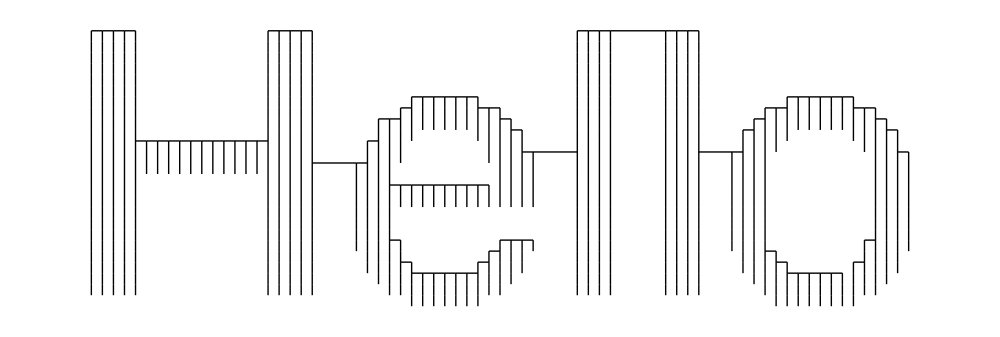

```mathematica
helloEMST=Graphics[{Thick,
Line[{{{2,-8},{2,-9}},{{2,-8},{3,-8}},{{3,-8},{3,-9}},{{3,-8},{4,-8}},{{4,-8},{4,-9}},{{4,-8},{5,-8}},{{5,-8},{5,-9}},{{5,-8},{6,-8}},{{6,-8},{6,-9}},{{18,-8},{18,-9}},{{18,-8},{19,-8}},{{19,-8},{19,-9}},{{19,-8},{20,-8}},{{20,-8},{20,-9}},{{20,-8},{21,-8}},{{21,-8},{21,-9}},{{21,-8},{22,-8}},{{22,-8},{22,-9}},{{46,-8},{46,-9}},{{46,-8},{47,-8}},{{47,-8},{48,-8}},{{47,-8},{47,-9}},{{48,-8},{48,-9}},{{48,-8},{49,-8}},{{49,-8},{49,-9}},{{54,-8},{54,-9}},{{54,-8},{55,-8}},{{55,-8},{55,-9}},{{55,-8},{56,-8}},{{56,-8},{56,-9}},{{56,-8},{57,-8}},{{57,-8},{57,-9}},{{2,-9},{2,-10}},{{3,-9},{3,-10}},{{4,-9},{4,-10}},{{5,-9},{5,-10}},{{6,-9},{6,-10}},{{18,-9},{18,-10}},{{19,-9},{19,-10}},{{20,-9},{20,-10}},{{21,-9},{21,-10}},{{22,-9},{22,-10}},{{46,-9},{46,-10}},{{47,-9},{47,-10}},{{48,-9},{48,-10}},{{49,-9},{49,-10}},{{54,-9},{54,-10}},{{55,-9},{55,-10}},{{56,-9},{56,-10}},{{57,-9},{57,-10}},{{2,-10},{2,-11}},{{3,-10},{3,-11}},{{4,-10},{4,-11}},{{5,-10},{5,-11}},{{6,-10},{6,-11}},{{18,-10},{18,-11}},{{19,-10},{19,-11}},{{20,-10},{20,-11}},{{21,-10},{21,-11}},{{22,-10},{22,-11}},{{46,-10},{46,-11}},{{47,-10},{47,-11}},{{48,-10},{48,-11}},{{49,-10},{49,-11}},{{54,-10},{54,-11}},{{55,-10},{55,-11}},{{56,-10},{56,-11}},{{57,-10},{57,-11}},{{2,-11},{2,-12}},{{3,-11},{3,-12}},{{4,-11},{4,-12}},{{5,-11},{5,-12}},{{6,-11},{6,-12}},{{18,-11},{18,-12}},{{19,-11},{19,-12}},{{20,-11},{20,-12}},{{21,-11},{21,-12}},{{22,-11},{22,-12}},{{46,-11},{46,-12}},{{47,-11},{47,-12}},{{48,-11},{48,-12}},{{49,-11},{49,-12}},{{54,-11},{54,-12}},{{55,-11},{55,-12}},{{56,-11},{56,-12}},{{57,-11},{57,-12}},{{2,-12},{2,-13}},{{3,-12},{3,-13}},{{4,-12},{4,-13}},{{5,-12},{5,-13}},{{6,-12},{6,-13}},{{18,-12},{18,-13}},{{19,-12},{19,-13}},{{20,-12},{20,-13}},{{21,-12},{21,-13}},{{22,-12},{22,-13}},{{46,-12},{46,-13}},{{47,-12},{47,-13}},{{48,-12},{48,-13}},{{49,-12},{49,-13}},{{54,-12},{54,-13}},{{55,-12},{55,-13}},{{56,-12},{56,-13}},{{57,-12},{57,-13}},{{2,-13},{2,-14}},{{3,-13},{3,-14}},{{4,-13},{4,-14}},{{5,-13},{5,-14}},{{6,-13},{6,-14}},{{18,-13},{18,-14}},{{19,-13},{19,-14}},{{20,-13},{20,-14}},{{21,-13},{21,-14}},{{22,-13},{22,-14}},{{46,-13},{46,-14}},{{47,-13},{47,-14}},{{48,-13},{48,-14}},{{49,-13},{49,-14}},{{54,-13},{54,-14}},{{55,-13},{55,-14}},{{56,-13},{56,-14}},{{57,-13},{57,-14}},{{2,-14},{2,-15}},{{3,-14},{3,-15}},{{4,-14},{4,-15}},{{5,-14},{5,-15}},{{6,-14},{6,-15}},{{18,-14},{18,-15}},{{19,-14},{19,-15}},{{20,-14},{20,-15}},{{21,-14},{21,-15}},{{22,-14},{22,-15}},{{31,-14},{32,-14}},{{31,-14},{31,-15}},{{32,-14},{32,-15}},{{32,-14},{33,-14}},{{33,-14},{34,-14}},{{33,-14},{33,-15}},{{34,-14},{34,-15}},{{34,-14},{35,-14}},{{35,-14},{35,-15}},{{35,-14},{36,-14}},{{36,-14},{36,-15}},{{36,-14},{37,-14}},{{37,-14},{37,-15}},{{46,-14},{46,-15}},{{47,-14},{47,-15}},{{48,-14},{48,-15}},{{49,-14},{49,-15}},{{54,-14},{54,-15}},{{55,-14},{55,-15}},{{56,-14},{56,-15}},{{57,-14},{57,-15}},{{65,-14},{65,-15}},{{65,-14},{66,-14}},{{66,-14},{66,-15}},{{66,-14},{67,-14}},{{67,-14},{67,-15}},{{67,-14},{68,-14}},{{68,-14},{68,-15}},{{68,-14},{69,-14}},{{69,-14},{69,-15}},{{69,-14},{70,-14}},{{70,-14},{71,-14}},{{70,-14},{70,-15}},{{71,-14},{71,-15}},{{2,-15},{2,-16}},{{3,-15},{3,-16}},{{4,-15},{4,-16}},{{5,-15},{5,-16}},{{6,-15},{6,-16}},{{18,-15},{18,-16}},{{19,-15},{19,-16}},{{20,-15},{20,-16}},{{21,-15},{21,-16}},{{22,-15},{22,-16}},{{30,-15},{31,-15}},{{30,-15},{30,-16}},{{31,-15},{31,-16}},{{32,-15},{32,-16}},{{33,-15},{33,-16}},{{34,-15},{34,-16}},{{35,-15},{35,-16}},{{36,-15},{36,-16}},{{37,-15},{38,-15}},{{37,-15},{37,-16}},{{38,-15},{38,-16}},{{38,-15},{39,-15}},{{39,-15},{39,-16}},{{46,-15},{46,-16}},{{47,-15},{47,-16}},{{48,-15},{48,-16}},{{49,-15},{49,-16}},{{54,-15},{54,-16}},{{55,-15},{55,-16}},{{56,-15},{56,-16}},{{57,-15},{57,-16}},{{63,-15},{63,-16}},{{63,-15},{64,-15}},{{64,-15},{64,-16}},{{64,-15},{65,-15}},{{65,-15},{65,-16}},{{66,-15},{66,-16}},{{67,-15},{67,-16}},{{68,-15},{68,-16}},{{69,-15},{69,-16}},{{70,-15},{70,-16}},{{71,-15},{71,-16}},{{71,-15},{72,-15}},{{72,-15},{73,-15}},{{72,-15},{72,-16}},{{73,-15},{73,-16}},{{2,-16},{2,-17}},{{3,-16},{3,-17}},{{4,-16},{4,-17}},{{5,-16},{5,-17}},{{6,-16},{6,-17}},{{18,-16},{18,-17}},{{19,-16},{19,-17}},{{20,-16},{20,-17}},{{21,-16},{21,-17}},{{22,-16},{22,-17}},{{28,-16},{28,-17}},{{28,-16},{29,-16}},{{29,-16},{30,-16}},{{29,-16},{29,-17}},{{30,-16},{30,-17}},{{31,-16},{31,-17}},{{32,-16},{32,-17}},{{33,-16},{33,-17}},{{34,-16},{34,-17}},{{35,-16},{35,-17}},{{36,-16},{36,-17}},{{37,-16},{37,-17}},{{38,-16},{38,-17}},{{39,-16},{39,-17}},{{39,-16},{40,-16}},{{40,-16},{40,-17}},{{46,-16},{46,-17}},{{47,-16},{47,-17}},{{48,-16},{48,-17}},{{49,-16},{49,-17}},{{54,-16},{54,-17}},{{55,-16},{55,-17}},{{56,-16},{56,-17}},{{57,-16},{57,-17}},{{62,-16},{62,-17}},{{62,-16},{63,-16}},{{63,-16},{63,-17}},{{64,-16},{64,-17}},{{65,-16},{65,-17}},{{66,-16},{66,-17}},{{67,-16},{67,-17}},{{68,-16},{68,-17}},{{69,-16},{69,-17}},{{70,-16},{70,-17}},{{71,-16},{71,-17}},{{72,-16},{72,-17}},{{73,-16},{73,-17}},{{73,-16},{74,-16}},{{74,-16},{74,-17}},{{2,-17},{2,-18}},{{3,-17},{3,-18}},{{4,-17},{4,-18}},{{5,-17},{5,-18}},{{6,-17},{6,-18}},{{18,-17},{18,-18}},{{19,-17},{19,-18}},{{20,-17},{20,-18}},{{21,-17},{21,-18}},{{22,-17},{22,-18}},{{28,-17},{28,-18}},{{29,-17},{29,-18}},{{30,-17},{30,-18}},{{31,-17},{31,-18}},{{37,-17},{37,-18}},{{38,-17},{38,-18}},{{39,-17},{39,-18}},{{40,-17},{41,-17}},{{40,-17},{40,-18}},{{41,-17},{41,-18}},{{46,-17},{46,-18}},{{47,-17},{47,-18}},{{48,-17},{48,-18}},{{49,-17},{49,-18}},{{54,-17},{54,-18}},{{55,-17},{55,-18}},{{56,-17},{56,-18}},{{57,-17},{57,-18}},{{61,-17},{61,-18}},{{61,-17},{62,-17}},{{62,-17},{62,-18}},{{63,-17},{63,-18}},{{64,-17},{64,-18}},{{65,-17},{65,-18}},{{71,-17},{71,-18}},{{72,-17},{72,-18}},{{73,-17},{73,-18}},{{74,-17},{75,-17}},{{74,-17},{74,-18}},{{75,-17},{75,-18}},{{2,-18},{2,-19}},{{3,-18},{3,-19}},{{4,-18},{4,-19}},{{5,-18},{5,-19}},{{6,-18},{6,-19}},{{6,-18},{7,-18}},{{7,-18},{7,-19}},{{7,-18},{8,-18}},{{8,-18},{9,-18}},{{8,-18},{8,-19}},{{9,-18},{10,-18}},{{9,-18},{9,-19}},{{10,-18},{10,-19}},{{10,-18},{11,-18}},{{11,-18},{11,-19}},{{11,-18},{12,-18}},{{12,-18},{12,-19}},{{12,-18},{13,-18}},{{13,-18},{13,-19}},{{13,-18},{14,-18}},{{14,-18},{14,-19}},{{14,-18},{15,-18}},{{15,-18},{15,-19}},{{15,-18},{16,-18}},{{16,-18},{16,-19}},{{16,-18},{17,-18}},{{17,-18},{17,-19}},{{17,-18},{18,-18}},{{18,-18},{18,-19}},{{19,-18},{19,-19}},{{20,-18},{20,-19}},{{21,-18},{21,-19}},{{22,-18},{22,-19}},{{27,-18},{27,-19}},{{27,-18},{28,-18}},{{28,-18},{28,-19}},{{29,-18},{29,-19}},{{30,-18},{30,-19}},{{38,-18},{38,-19}},{{39,-18},{39,-19}},{{40,-18},{40,-19}},{{41,-18},{41,-19}},{{46,-18},{46,-19}},{{47,-18},{47,-19}},{{48,-18},{48,-19}},{{49,-18},{49,-19}},{{54,-18},{54,-19}},{{55,-18},{55,-19}},{{56,-18},{56,-19}},{{57,-18},{57,-19}},{{61,-18},{61,-19}},{{62,-18},{62,-19}},{{63,-18},{63,-19}},{{64,-18},{64,-19}},{{72,-18},{72,-19}},{{73,-18},{73,-19}},{{74,-18},{74,-19}},{{75,-18},{75,-19}},{{2,-19},{2,-20}},{{3,-19},{3,-20}},{{4,-19},{4,-20}},{{5,-19},{5,-20}},{{6,-19},{6,-20}},{{7,-19},{7,-20}},{{8,-19},{8,-20}},{{9,-19},{9,-20}},{{10,-19},{10,-20}},{{11,-19},{11,-20}},{{12,-19},{12,-20}},{{13,-19},{13,-20}},{{14,-19},{14,-20}},{{15,-19},{15,-20}},{{16,-19},{16,-20}},{{17,-19},{17,-20}},{{18,-19},{18,-20}},{{19,-19},{19,-20}},{{20,-19},{20,-20}},{{21,-19},{21,-20}},{{22,-19},{22,-20}},{{27,-19},{27,-20}},{{28,-19},{28,-20}},{{29,-19},{29,-20}},{{30,-19},{30,-20}},{{38,-19},{38,-20}},{{39,-19},{39,-20}},{{40,-19},{40,-20}},{{41,-19},{41,-20}},{{41,-19},{42,-19}},{{42,-19},{42,-20}},{{46,-19},{46,-20}},{{47,-19},{47,-20}},{{48,-19},{48,-20}},{{49,-19},{49,-20}},{{54,-19},{54,-20}},{{55,-19},{55,-20}},{{56,-19},{56,-20}},{{57,-19},{57,-20}},{{60,-19},{60,-20}},{{60,-19},{61,-19}},{{61,-19},{61,-20}},{{62,-19},{62,-20}},{{63,-19},{63,-20}},{{73,-19},{73,-20}},{{74,-19},{74,-20}},{{75,-19},{75,-20}},{{75,-19},{76,-19}},{{76,-19},{76,-20}},{{2,-20},{2,-21}},{{3,-20},{3,-21}},{{4,-20},{4,-21}},{{5,-20},{5,-21}},{{6,-20},{6,-21}},{{7,-20},{7,-21}},{{8,-20},{8,-21}},{{9,-20},{9,-21}},{{10,-20},{10,-21}},{{11,-20},{11,-21}},{{12,-20},{12,-21}},{{13,-20},{13,-21}},{{14,-20},{14,-21}},{{15,-20},{15,-21}},{{16,-20},{16,-21}},{{17,-20},{17,-21}},{{18,-20},{18,-21}},{{19,-20},{19,-21}},{{20,-20},{20,-21}},{{21,-20},{21,-21}},{{22,-20},{22,-21}},{{26,-20},{26,-21}},{{26,-20},{27,-20}},{{27,-20},{27,-21}},{{28,-20},{28,-21}},{{29,-20},{29,-21}},{{39,-20},{39,-21}},{{40,-20},{40,-21}},{{41,-20},{41,-21}},{{42,-20},{42,-21}},{{46,-20},{46,-21}},{{47,-20},{47,-21}},{{48,-20},{48,-21}},{{49,-20},{49,-21}},{{54,-20},{54,-21}},{{55,-20},{55,-21}},{{56,-20},{56,-21}},{{57,-20},{57,-21}},{{60,-20},{60,-21}},{{61,-20},{61,-21}},{{62,-20},{62,-21}},{{63,-20},{63,-21}},{{73,-20},{73,-21}},{{74,-20},{74,-21}},{{75,-20},{75,-21}},{{76,-20},{76,-21}},{{2,-21},{2,-22}},{{3,-21},{3,-22}},{{4,-21},{4,-22}},{{5,-21},{5,-22}},{{6,-21},{6,-22}},{{18,-21},{18,-22}},{{19,-21},{19,-22}},{{20,-21},{20,-22}},{{21,-21},{21,-22}},{{22,-21},{22,-22}},{{26,-21},{26,-22}},{{27,-21},{27,-22}},{{28,-21},{28,-22}},{{29,-21},{29,-22}},{{39,-21},{39,-22}},{{40,-21},{40,-22}},{{41,-21},{41,-22}},{{42,-21},{42,-22}},{{46,-21},{46,-22}},{{47,-21},{47,-22}},{{48,-21},{48,-22}},{{49,-21},{49,-22}},{{54,-21},{54,-22}},{{55,-21},{55,-22}},{{56,-21},{56,-22}},{{57,-21},{57,-22}},{{60,-21},{60,-22}},{{61,-21},{61,-22}},{{62,-21},{62,-22}},{{63,-21},{63,-22}},{{73,-21},{73,-22}},{{74,-21},{74,-22}},{{75,-21},{75,-22}},{{76,-21},{76,-22}},{{2,-22},{2,-23}},{{3,-22},{3,-23}},{{4,-22},{4,-23}},{{5,-22},{5,-23}},{{6,-22},{6,-23}},{{18,-22},{18,-23}},{{19,-22},{19,-23}},{{20,-22},{20,-23}},{{21,-22},{21,-23}},{{22,-22},{22,-23}},{{26,-22},{26,-23}},{{27,-22},{27,-23}},{{28,-22},{28,-23}},{{29,-22},{29,-23}},{{29,-22},{30,-22}},{{30,-22},{31,-22}},{{30,-22},{30,-23}},{{31,-22},{32,-22}},{{31,-22},{31,-23}},{{32,-22},{32,-23}},{{32,-22},{33,-22}},{{33,-22},{33,-23}},{{33,-22},{34,-22}},{{34,-22},{34,-23}},{{34,-22},{35,-22}},{{35,-22},{35,-23}},{{35,-22},{36,-22}},{{36,-22},{37,-22}},{{36,-22},{36,-23}},{{37,-22},{38,-22}},{{37,-22},{37,-23}},{{38,-22},{38,-23}},{{39,-22},{39,-23}},{{40,-22},{40,-23}},{{41,-22},{41,-23}},{{42,-22},{42,-23}},{{46,-22},{46,-23}},{{47,-22},{47,-23}},{{48,-22},{48,-23}},{{49,-22},{49,-23}},{{54,-22},{54,-23}},{{55,-22},{55,-23}},{{56,-22},{56,-23}},{{57,-22},{57,-23}},{{60,-22},{60,-23}},{{61,-22},{61,-23}},{{62,-22},{62,-23}},{{63,-22},{63,-23}},{{73,-22},{73,-23}},{{74,-22},{74,-23}},{{75,-22},{75,-23}},{{76,-22},{76,-23}},{{2,-23},{2,-24}},{{3,-23},{3,-24}},{{4,-23},{4,-24}},{{5,-23},{5,-24}},{{6,-23},{6,-24}},{{18,-23},{18,-24}},{{19,-23},{19,-24}},{{20,-23},{20,-24}},{{21,-23},{21,-24}},{{22,-23},{22,-24}},{{26,-23},{26,-24}},{{27,-23},{27,-24}},{{28,-23},{28,-24}},{{29,-23},{29,-24}},{{30,-23},{30,-24}},{{31,-23},{31,-24}},{{32,-23},{32,-24}},{{33,-23},{33,-24}},{{34,-23},{34,-24}},{{35,-23},{35,-24}},{{36,-23},{36,-24}},{{37,-23},{37,-24}},{{38,-23},{38,-24}},{{39,-23},{39,-24}},{{40,-23},{40,-24}},{{41,-23},{41,-24}},{{42,-23},{42,-24}},{{46,-23},{46,-24}},{{47,-23},{47,-24}},{{48,-23},{48,-24}},{{49,-23},{49,-24}},{{54,-23},{54,-24}},{{55,-23},{55,-24}},{{56,-23},{56,-24}},{{57,-23},{57,-24}},{{60,-23},{60,-24}},{{61,-23},{61,-24}},{{62,-23},{62,-24}},{{63,-23},{63,-24}},{{73,-23},{73,-24}},{{74,-23},{74,-24}},{{75,-23},{75,-24}},{{76,-23},{76,-24}},{{2,-24},{2,-25}},{{3,-24},{3,-25}},{{4,-24},{4,-25}},{{5,-24},{5,-25}},{{6,-24},{6,-25}},{{18,-24},{18,-25}},{{19,-24},{19,-25}},{{20,-24},{20,-25}},{{21,-24},{21,-25}},{{22,-24},{22,-25}},{{26,-24},{26,-25}},{{27,-24},{27,-25}},{{28,-24},{28,-25}},{{29,-24},{29,-25}},{{46,-24},{46,-25}},{{47,-24},{47,-25}},{{48,-24},{48,-25}},{{49,-24},{49,-25}},{{54,-24},{54,-25}},{{55,-24},{55,-25}},{{56,-24},{56,-25}},{{57,-24},{57,-25}},{{60,-24},{60,-25}},{{61,-24},{61,-25}},{{62,-24},{62,-25}},{{63,-24},{63,-25}},{{73,-24},{73,-25}},{{74,-24},{74,-25}},{{75,-24},{75,-25}},{{76,-24},{76,-25}},{{2,-25},{2,-26}},{{3,-25},{3,-26}},{{4,-25},{4,-26}},{{5,-25},{5,-26}},{{6,-25},{6,-26}},{{18,-25},{18,-26}},{{19,-25},{19,-26}},{{20,-25},{20,-26}},{{21,-25},{21,-26}},{{22,-25},{22,-26}},{{26,-25},{26,-26}},{{27,-25},{27,-26}},{{28,-25},{28,-26}},{{29,-25},{29,-26}},{{46,-25},{46,-26}},{{47,-25},{47,-26}},{{48,-25},{48,-26}},{{49,-25},{49,-26}},{{54,-25},{54,-26}},{{55,-25},{55,-26}},{{56,-25},{56,-26}},{{57,-25},{57,-26}},{{60,-25},{60,-26}},{{61,-25},{61,-26}},{{62,-25},{62,-26}},{{63,-25},{63,-26}},{{73,-25},{73,-26}},{{74,-25},{74,-26}},{{75,-25},{75,-26}},{{76,-25},{76,-26}},{{2,-26},{2,-27}},{{3,-26},{3,-27}},{{4,-26},{4,-27}},{{5,-26},{5,-27}},{{6,-26},{6,-27}},{{18,-26},{18,-27}},{{19,-26},{19,-27}},{{20,-26},{20,-27}},{{21,-26},{21,-27}},{{22,-26},{22,-27}},{{26,-26},{26,-27}},{{27,-26},{27,-27}},{{28,-26},{28,-27}},{{29,-26},{29,-27}},{{46,-26},{46,-27}},{{47,-26},{47,-27}},{{48,-26},{48,-27}},{{49,-26},{49,-27}},{{54,-26},{54,-27}},{{55,-26},{55,-27}},{{56,-26},{56,-27}},{{57,-26},{57,-27}},{{60,-26},{60,-27}},{{61,-26},{61,-27}},{{62,-26},{62,-27}},{{63,-26},{63,-27}},{{73,-26},{73,-27}},{{74,-26},{74,-27}},{{75,-26},{75,-27}},{{76,-26},{76,-27}},{{2,-27},{2,-28}},{{3,-27},{3,-28}},{{4,-27},{4,-28}},{{5,-27},{5,-28}},{{6,-27},{6,-28}},{{18,-27},{18,-28}},{{19,-27},{19,-28}},{{20,-27},{20,-28}},{{21,-27},{21,-28}},{{22,-27},{22,-28}},{{26,-27},{26,-28}},{{27,-27},{27,-28}},{{28,-27},{28,-28}},{{29,-27},{29,-28}},{{29,-27},{30,-27}},{{30,-27},{30,-28}},{{39,-27},{40,-27}},{{39,-27},{39,-28}},{{40,-27},{41,-27}},{{40,-27},{40,-28}},{{41,-27},{42,-27}},{{41,-27},{41,-28}},{{42,-27},{42,-28}},{{46,-27},{46,-28}},{{47,-27},{47,-28}},{{48,-27},{48,-28}},{{49,-27},{49,-28}},{{54,-27},{54,-28}},{{55,-27},{55,-28}},{{56,-27},{56,-28}},{{57,-27},{57,-28}},{{60,-27},{60,-28}},{{61,-27},{61,-28}},{{62,-27},{62,-28}},{{63,-27},{63,-28}},{{72,-27},{72,-28}},{{72,-27},{73,-27}},{{73,-27},{73,-28}},{{74,-27},{74,-28}},{{75,-27},{75,-28}},{{76,-27},{76,-28}},{{2,-28},{2,-29}},{{3,-28},{3,-29}},{{4,-28},{4,-29}},{{5,-28},{5,-29}},{{6,-28},{6,-29}},{{18,-28},{18,-29}},{{19,-28},{19,-29}},{{20,-28},{20,-29}},{{21,-28},{21,-29}},{{22,-28},{22,-29}},{{27,-28},{27,-29}},{{28,-28},{28,-29}},{{29,-28},{29,-29}},{{30,-28},{30,-29}},{{38,-28},{39,-28}},{{38,-28},{38,-29}},{{39,-28},{39,-29}},{{40,-28},{40,-29}},{{41,-28},{41,-29}},{{46,-28},{46,-29}},{{47,-28},{47,-29}},{{48,-28},{48,-29}},{{49,-28},{49,-29}},{{54,-28},{54,-29}},{{55,-28},{55,-29}},{{56,-28},{56,-29}},{{57,-28},{57,-29}},{{61,-28},{61,-29}},{{62,-28},{62,-29}},{{63,-28},{64,-28}},{{63,-28},{63,-29}},{{64,-28},{64,-29}},{{72,-28},{72,-29}},{{73,-28},{73,-29}},{{74,-28},{74,-29}},{{75,-28},{75,-29}},{{2,-29},{2,-30}},{{3,-29},{3,-30}},{{4,-29},{4,-30}},{{5,-29},{5,-30}},{{6,-29},{6,-30}},{{18,-29},{18,-30}},{{19,-29},{19,-30}},{{20,-29},{20,-30}},{{21,-29},{21,-30}},{{22,-29},{22,-30}},{{27,-29},{27,-30}},{{28,-29},{28,-30}},{{29,-29},{29,-30}},{{30,-29},{31,-29}},{{30,-29},{30,-30}},{{31,-29},{31,-30}},{{37,-29},{38,-29}},{{37,-29},{37,-30}},{{38,-29},{38,-30}},{{39,-29},{39,-30}},{{40,-29},{40,-30}},{{41,-29},{41,-30}},{{46,-29},{46,-30}},{{47,-29},{47,-30}},{{48,-29},{48,-30}},{{49,-29},{49,-30}},{{54,-29},{54,-30}},{{55,-29},{55,-30}},{{56,-29},{56,-30}},{{57,-29},{57,-30}},{{61,-29},{61,-30}},{{62,-29},{62,-30}},{{63,-29},{63,-30}},{{64,-29},{64,-30}},{{64,-29},{65,-29}},{{65,-29},{65,-30}},{{71,-29},{71,-30}},{{71,-29},{72,-29}},{{72,-29},{72,-30}},{{73,-29},{73,-30}},{{74,-29},{74,-30}},{{75,-29},{75,-30}},{{2,-30},{2,-31}},{{3,-30},{3,-31}},{{4,-30},{4,-31}},{{5,-30},{5,-31}},{{6,-30},{6,-31}},{{18,-30},{18,-31}},{{19,-30},{19,-31}},{{20,-30},{20,-31}},{{21,-30},{21,-31}},{{22,-30},{22,-31}},{{28,-30},{28,-31}},{{29,-30},{29,-31}},{{30,-30},{30,-31}},{{31,-30},{32,-30}},{{31,-30},{31,-31}},{{32,-30},{32,-31}},{{32,-30},{33,-30}},{{33,-30},{33,-31}},{{33,-30},{34,-30}},{{34,-30},{35,-30}},{{34,-30},{34,-31}},{{35,-30},{36,-30}},{{35,-30},{35,-31}},{{36,-30},{37,-30}},{{36,-30},{36,-31}},{{37,-30},{37,-31}},{{38,-30},{38,-31}},{{39,-30},{39,-31}},{{40,-30},{40,-31}},{{46,-30},{46,-31}},{{47,-30},{47,-31}},{{48,-30},{48,-31}},{{49,-30},{49,-31}},{{54,-30},{54,-31}},{{55,-30},{55,-31}},{{56,-30},{56,-31}},{{57,-30},{57,-31}},{{62,-30},{62,-31}},{{63,-30},{63,-31}},{{64,-30},{64,-31}},{{65,-30},{66,-30}},{{65,-30},{65,-31}},{{66,-30},{67,-30}},{{66,-30},{66,-31}},{{67,-30},{68,-30}},{{67,-30},{67,-31}},{{68,-30},{69,-30}},{{68,-30},{68,-31}},{{69,-30},{70,-30}},{{69,-30},{69,-31}},{{70,-30},{70,-31}},{{71,-30},{71,-31}},{{72,-30},{72,-31}},{{73,-30},{73,-31}},{{74,-30},{74,-31}},{{2,-31},{2,-32}},{{3,-31},{3,-32}},{{4,-31},{4,-32}},{{5,-31},{5,-32}},{{6,-31},{6,-32}},{{18,-31},{18,-32}},{{19,-31},{19,-32}},{{20,-31},{20,-32}},{{21,-31},{21,-32}},{{22,-31},{22,-32}},{{29,-31},{29,-32}},{{30,-31},{30,-32}},{{31,-31},{31,-32}},{{32,-31},{32,-32}},{{33,-31},{33,-32}},{{34,-31},{34,-32}},{{35,-31},{35,-32}},{{36,-31},{36,-32}},{{37,-31},{37,-32}},{{38,-31},{38,-32}},{{39,-31},{39,-32}},{{46,-31},{46,-32}},{{47,-31},{47,-32}},{{48,-31},{48,-32}},{{49,-31},{49,-32}},{{54,-31},{54,-32}},{{55,-31},{55,-32}},{{56,-31},{56,-32}},{{57,-31},{57,-32}},{{63,-31},{63,-32}},{{64,-31},{64,-32}},{{65,-31},{65,-32}},{{66,-31},{66,-32}},{{67,-31},{67,-32}},{{68,-31},{68,-32}},{{69,-31},{69,-32}},{{70,-31},{70,-32}},{{71,-31},{71,-32}},{{72,-31},{72,-32}},{{73,-31},{73,-32}},{{31,-32},{31,-33}},{{32,-32},{32,-33}},{{33,-32},{33,-33}},{{34,-32},{34,-33}},{{35,-32},{35,-33}},{{36,-32},{36,-33}},{{37,-32},{37,-33}},{{64,-32},{64,-33}},{{65,-32},{65,-33}},{{66,-32},{66,-33}},{{67,-32},{67,-33}},{{68,-32},{68,-33}},{{69,-32},{69,-33}},{{70,-32},{70,-33}},{{71,-32},{71,-33}},{{57,-19},{60,-19}},{{42,-19},{46,-19}},{{22,-20},{26,-20}},{{49,-8},{54,-8}}}]},PlotRangePadding->None,ImageSize->1000]
```

```mathematica
Export[path<>"helloEMST.eps",helloEMST];
```

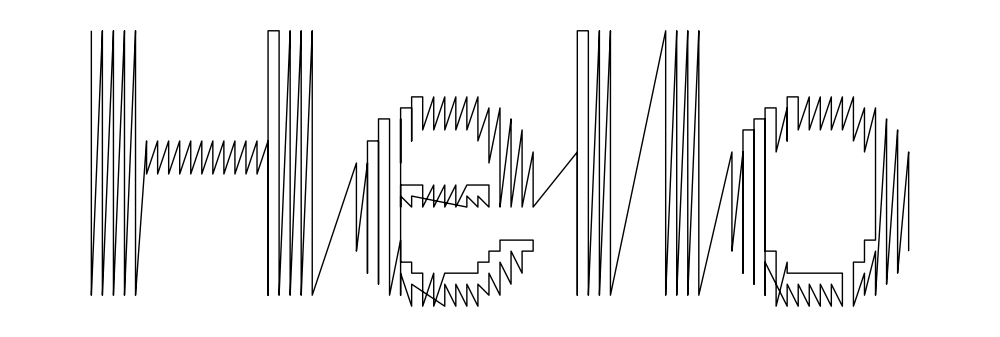

```mathematica
helloInit=Graphics[{Thick,
Line[{{2,-8},{2,-9},{2,-10},{2,-11},{2,-12},{2,-13},{2,-14},{2,-15},{2,-16},{2,-17},{2,-18},{2,-19},{2,-20},{2,-21},{2,-22},{2,-23},{2,-24},{2,-25},{2,-26},{2,-27},{2,-28},{2,-29},{2,-30},{2,-31},{2,-32},{3,-8},{3,-9},{3,-10},{3,-11},{3,-12},{3,-13},{3,-14},{3,-15},{3,-16},{3,-17},{3,-18},{3,-19},{3,-20},{3,-21},{3,-22},{3,-23},{3,-24},{3,-25},{3,-26},{3,-27},{3,-28},{3,-29},{3,-30},{3,-31},{3,-32},{4,-8},{4,-9},{4,-10},{4,-11},{4,-12},{4,-13},{4,-14},{4,-15},{4,-16},{4,-17},{4,-18},{4,-19},{4,-20},{4,-21},{4,-22},{4,-23},{4,-24},{4,-25},{4,-26},{4,-27},{4,-28},{4,-29},{4,-30},{4,-31},{4,-32},{5,-8},{5,-9},{5,-10},{5,-11},{5,-12},{5,-13},{5,-14},{5,-15},{5,-16},{5,-17},{5,-18},{5,-19},{5,-20},{5,-21},{5,-22},{5,-23},{5,-24},{5,-25},{5,-26},{5,-27},{5,-28},{5,-29},{5,-30},{5,-31},{5,-32},{6,-8},{6,-9},{6,-10},{6,-11},{6,-12},{6,-13},{6,-14},{6,-15},{6,-16},{6,-17},{6,-18},{6,-19},{6,-20},{6,-21},{6,-22},{6,-23},{6,-24},{6,-25},{6,-26},{6,-27},{6,-28},{6,-29},{6,-30},{6,-31},{6,-32},{7,-18},{7,-19},{7,-20},{7,-21},{8,-18},{8,-19},{8,-20},{8,-21},{9,-18},{9,-19},{9,-20},{9,-21},{10,-18},{10,-19},{10,-20},{10,-21},{11,-18},{11,-19},{11,-20},{11,-21},{12,-18},{12,-19},{12,-20},{12,-21},{13,-18},{13,-19},{13,-20},{13,-21},{14,-18},{14,-19},{14,-20},{14,-21},{15,-18},{15,-19},{15,-20},{15,-21},{16,-18},{16,-19},{16,-20},{16,-21},{17,-18},{17,-19},{17,-20},{17,-21},{18,-18},{18,-19},{18,-20},{18,-21},{18,-22},{18,-23},{18,-24},{18,-25},{18,-26},{18,-27},{18,-28},{18,-29},{18,-30},{18,-31},{18,-32},{18,-17},{18,-16},{18,-15},{18,-14},{18,-13},{18,-12},{18,-11},{18,-10},{18,-9},{18,-8},{19,-8},{19,-9},{19,-10},{19,-11},{19,-12},{19,-13},{19,-14},{19,-15},{19,-16},{19,-17},{19,-18},{19,-19},{19,-20},{19,-21},{19,-22},{19,-23},{19,-24},{19,-25},{19,-26},{19,-27},{19,-28},{19,-29},{19,-30},{19,-31},{19,-32},{20,-8},{20,-9},{20,-10},{20,-11},{20,-12},{20,-13},{20,-14},{20,-15},{20,-16},{20,-17},{20,-18},{20,-19},{20,-20},{20,-21},{20,-22},{20,-23},{20,-24},{20,-25},{20,-26},{20,-27},{20,-28},{20,-29},{20,-30},{20,-31},{20,-32},{21,-8},{21,-9},{21,-10},{21,-11},{21,-12},{21,-13},{21,-14},{21,-15},{21,-16},{21,-17},{21,-18},{21,-19},{21,-20},{21,-21},{21,-22},{21,-23},{21,-24},{21,-25},{21,-26},{21,-27},{21,-28},{21,-29},{21,-30},{21,-31},{21,-32},{22,-8},{22,-9},{22,-10},{22,-11},{22,-12},{22,-13},{22,-14},{22,-15},{22,-16},{22,-17},{22,-18},{22,-19},{22,-20},{22,-21},{22,-22},{22,-23},{22,-24},{22,-25},{22,-26},{22,-27},{22,-28},{22,-29},{22,-30},{22,-31},{22,-32},{26,-20},{26,-21},{26,-22},{26,-23},{26,-24},{26,-25},{26,-26},{26,-27},{26,-28},{27,-20},{27,-21},{27,-22},{27,-23},{27,-24},{27,-25},{27,-26},{27,-27},{27,-28},{27,-29},{27,-30},{27,-19},{27,-18},{28,-18},{28,-19},{28,-20},{28,-21},{28,-22},{28,-23},{28,-24},{28,-25},{28,-26},{28,-27},{28,-28},{28,-29},{28,-30},{28,-31},{28,-17},{28,-16},{29,-16},{29,-17},{29,-18},{29,-19},{29,-20},{29,-21},{29,-22},{29,-23},{29,-24},{29,-25},{29,-26},{29,-27},{29,-28},{29,-29},{29,-30},{29,-31},{29,-32},{30,-27},{30,-28},{30,-29},{31,-29},{31,-30},{32,-30},{32,-31},{32,-32},{32,-33},{33,-30},{33,-31},{33,-32},{33,-33},{34,-30},{35,-30},{36,-30},{37,-30},{37,-29},{38,-29},{38,-28},{39,-28},{39,-27},{40,-27},{41,-27},{42,-27},{42,-28},{41,-28},{41,-29},{41,-30},{40,-28},{40,-29},{40,-30},{40,-31},{39,-29},{39,-30},{39,-31},{39,-32},{38,-30},{38,-31},{38,-32},{37,-31},{37,-32},{37,-33},{36,-31},{36,-32},{36,-33},{35,-31},{35,-32},{35,-33},{34,-31},{34,-32},{34,-33},{31,-31},{31,-32},{31,-33},{30,-30},{30,-31},{30,-32},{30,-22},{31,-22},{32,-22},{32,-23},{32,-24},{33,-22},{33,-23},{33,-24},{34,-22},{34,-23},{34,-24},{35,-22},{35,-23},{35,-24},{36,-22},{37,-22},{38,-22},{38,-23},{38,-24},{37,-23},{37,-24},{36,-23},{36,-24},{31,-23},{31,-24},{30,-23},{30,-24},{30,-16},{30,-17},{30,-18},{30,-19},{30,-20},{30,-15},{31,-15},{31,-16},{31,-17},{31,-18},{31,-14},{32,-14},{32,-15},{32,-16},{32,-17},{33,-14},{33,-15},{33,-16},{33,-17},{34,-14},{34,-15},{34,-16},{34,-17},{35,-14},{35,-15},{35,-16},{35,-17},{36,-14},{36,-15},{36,-16},{36,-17},{37,-14},{37,-15},{37,-16},{37,-17},{37,-18},{38,-15},{38,-16},{38,-17},{38,-18},{38,-19},{38,-20},{39,-15},{39,-16},{39,-17},{39,-18},{39,-19},{39,-20},{39,-21},{39,-22},{39,-23},{39,-24},{40,-16},{40,-17},{40,-18},{40,-19},{40,-20},{40,-21},{40,-22},{40,-23},{40,-24},{41,-17},{41,-18},{41,-19},{41,-20},{41,-21},{41,-22},{41,-23},{41,-24},{42,-19},{42,-20},{42,-21},{42,-22},{42,-23},{42,-24},{46,-19},{46,-20},{46,-21},{46,-22},{46,-23},{46,-24},{46,-25},{46,-26},{46,-27},{46,-28},{46,-29},{46,-30},{46,-31},{46,-32},{46,-18},{46,-17},{46,-16},{46,-15},{46,-14},{46,-13},{46,-12},{46,-11},{46,-10},{46,-9},{46,-8},{47,-8},{47,-9},{47,-10},{47,-11},{47,-12},{47,-13},{47,-14},{47,-15},{47,-16},{47,-17},{47,-18},{47,-19},{47,-20},{47,-21},{47,-22},{47,-23},{47,-24},{47,-25},{47,-26},{47,-27},{47,-28},{47,-29},{47,-30},{47,-31},{47,-32},{48,-8},{48,-9},{48,-10},{48,-11},{48,-12},{48,-13},{48,-14},{48,-15},{48,-16},{48,-17},{48,-18},{48,-19},{48,-20},{48,-21},{48,-22},{48,-23},{48,-24},{48,-25},{48,-26},{48,-27},{48,-28},{48,-29},{48,-30},{48,-31},{48,-32},{49,-8},{49,-9},{49,-10},{49,-11},{49,-12},{49,-13},{49,-14},{49,-15},{49,-16},{49,-17},{49,-18},{49,-19},{49,-20},{49,-21},{49,-22},{49,-23},{49,-24},{49,-25},{49,-26},{49,-27},{49,-28},{49,-29},{49,-30},{49,-31},{49,-32},{54,-8},{54,-9},{54,-10},{54,-11},{54,-12},{54,-13},{54,-14},{54,-15},{54,-16},{54,-17},{54,-18},{54,-19},{54,-20},{54,-21},{54,-22},{54,-23},{54,-24},{54,-25},{54,-26},{54,-27},{54,-28},{54,-29},{54,-30},{54,-31},{54,-32},{55,-8},{55,-9},{55,-10},{55,-11},{55,-12},{55,-13},{55,-14},{55,-15},{55,-16},{55,-17},{55,-18},{55,-19},{55,-20},{55,-21},{55,-22},{55,-23},{55,-24},{55,-25},{55,-26},{55,-27},{55,-28},{55,-29},{55,-30},{55,-31},{55,-32},{56,-8},{56,-9},{56,-10},{56,-11},{56,-12},{56,-13},{56,-14},{56,-15},{56,-16},{56,-17},{56,-18},{56,-19},{56,-20},{56,-21},{56,-22},{56,-23},{56,-24},{56,-25},{56,-26},{56,-27},{56,-28},{56,-29},{56,-30},{56,-31},{56,-32},{57,-8},{57,-9},{57,-10},{57,-11},{57,-12},{57,-13},{57,-14},{57,-15},{57,-16},{57,-17},{57,-18},{57,-19},{57,-20},{57,-21},{57,-22},{57,-23},{57,-24},{57,-25},{57,-26},{57,-27},{57,-28},{57,-29},{57,-30},{57,-31},{57,-32},{60,-19},{60,-20},{60,-21},{60,-22},{60,-23},{60,-24},{60,-25},{60,-26},{60,-27},{60,-28},{61,-19},{61,-20},{61,-21},{61,-22},{61,-23},{61,-24},{61,-25},{61,-26},{61,-27},{61,-28},{61,-29},{61,-30},{61,-18},{61,-17},{62,-17},{62,-18},{62,-19},{62,-20},{62,-21},{62,-22},{62,-23},{62,-24},{62,-25},{62,-26},{62,-27},{62,-28},{62,-29},{62,-30},{62,-31},{62,-16},{63,-16},{63,-17},{63,-18},{63,-19},{63,-20},{63,-21},{63,-22},{63,-23},{63,-24},{63,-25},{63,-26},{63,-27},{63,-28},{64,-28},{64,-29},{64,-30},{64,-31},{64,-32},{64,-33},{65,-29},{65,-30},{66,-30},{67,-30},{68,-30},{69,-30},{70,-30},{70,-31},{70,-32},{70,-33},{69,-31},{69,-32},{69,-33},{68,-31},{68,-32},{68,-33},{67,-31},{67,-32},{67,-33},{66,-31},{66,-32},{66,-33},{65,-31},{65,-32},{65,-33},{63,-29},{63,-30},{63,-31},{63,-32},{63,-15},{64,-15},{64,-16},{64,-17},{64,-18},{64,-19},{65,-15},{65,-16},{65,-17},{65,-18},{65,-14},{66,-14},{66,-15},{66,-16},{66,-17},{67,-14},{67,-15},{67,-16},{67,-17},{68,-14},{68,-15},{68,-16},{68,-17},{69,-14},{69,-15},{69,-16},{69,-17},{70,-14},{70,-15},{70,-16},{70,-17},{71,-14},{71,-15},{71,-16},{71,-17},{71,-18},{72,-15},{72,-16},{72,-17},{72,-18},{72,-19},{73,-15},{73,-16},{73,-17},{73,-18},{73,-19},{73,-20},{73,-21},{73,-22},{73,-23},{73,-24},{73,-25},{73,-26},{73,-27},{72,-27},{72,-28},{72,-29},{71,-29},{71,-30},{71,-31},{71,-32},{71,-33},{72,-30},{72,-31},{72,-32},{73,-28},{73,-29},{73,-30},{73,-31},{73,-32},{74,-16},{74,-17},{74,-18},{74,-19},{74,-20},{74,-21},{74,-22},{74,-23},{74,-24},{74,-25},{74,-26},{74,-27},{74,-28},{74,-29},{74,-30},{74,-31},{75,-17},{75,-18},{75,-19},{75,-20},{75,-21},{75,-22},{75,-23},{75,-24},{75,-25},{75,-26},{75,-27},{75,-28},{75,-29},{75,-30},{76,-19},{76,-20},{76,-21},{76,-22},{76,-23},{76,-24},{76,-25},{76,-26},{76,-27},{76,-28}}]},PlotRangePadding->None,ImageSize->1000]
```

```mathematica
Export[path<>"helloInit.eps",helloInit];
```